# Transfer Function

```mathematica
Quit[]
```

## Mock Data

### Packages

```mathematica
SetDirectory[NotebookDirectory[]];
<<ErrorBarPlots`
<<MaTeX` (* Package to make plots with LaTeX fonts *)
LaunchKernels[]; (* To use all the available kernels *)
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

### Data

```mathematica
DataGraΦz0=Import["DataGraTz0.txt","Data"]//Quiet; (* Data from CLASS (python): {k, ωb, ωm} *)
Length[DataGraΦz0]/114//N (* There are 16 lists *)
PartData=Partition[DataGraΦz0,114]; (* Partition of data to consider each cosmology, i.e. each pair {ωb, ωm}*)
(* Modify data to get a squared normalized T(k) *)
NormPartData=Table[{#⟦1⟧,#⟦2⟧,#⟦3⟧,((#⟦4⟧)/Max[PartData⟦i,1,4⟧])^2}&/@PartData⟦i⟧,{i,1,Length[PartData]}]; 
MockData=Join@@NormPartData; (* Re-Join the datasets *)
Dimensions[MockData]
```

16.

{1824,4}

### Plots

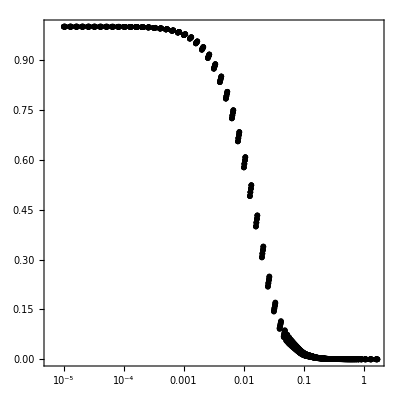

```mathematica
(* Plot of the 16 considered T(k)^2 *)
SamplePlotI=ListLogLinearPlot[Table[{MockData⟦i,1⟧,MockData⟦i,4⟧},{i,1,Length[MockData]}],PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T^2(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Thick,Black,PointSize[0.01]},AspectRatio->1]
```

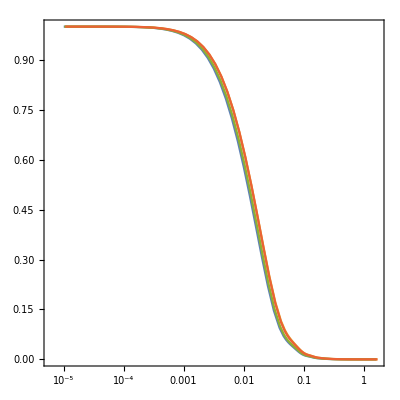

```mathematica
(* Same plot as above, but Joined -> See Fig. 4 *)
Sample1=Table[{NormPartData⟦1⟧⟦i,1⟧,NormPartData⟦1⟧⟦i,4⟧},{i,1,Length[NormPartData⟦1⟧]}];
Sample2=Table[{NormPartData⟦4⟧⟦i,1⟧,NormPartData⟦4⟧⟦i,4⟧},{i,1,Length[NormPartData⟦6⟧]}];
Sample3=Table[{NormPartData⟦10⟧⟦i,1⟧,NormPartData⟦10⟧⟦i,4⟧},{i,1,Length[NormPartData⟦10⟧]}];
Sample4=Table[{NormPartData⟦16⟧⟦i,1⟧,NormPartData⟦16⟧⟦i,4⟧},{i,1,Length[NormPartData⟦16⟧]}];
SamplePlotII=ListLogLinearPlot[{Sample1,Sample2,Sample3,Sample4},Joined->True,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T^2(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\{0.0214, 0.130\\}"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\{0.0220, 0.136\\}"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\{0.0227, 0.136\\}"],
(MaTeX[#,Magnification->1.2]&)/@Style["\\{0.0234, 0.150\\}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5}],
{0.25,0.2}],
Epilog->{Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\{\\omega_b, \\omega_m\\}"], Scaled[{0.285, 0.41}]]}]
```

```mathematica
(* Export data *)
Export["Gra_Transfer_Function_Data.txt",MockData,"Table"];
```

## Genetic Algorithm

## Grammar, Fitness Function, and Genetic Instructions

### Grammar

```mathematica
(* Possible operations. The proposal grammar depends on each specific problem *)
poly[x_]:=x

grammar={poly}; (* Array of operations *)
```

### Genetic Code

```mathematica
length=8; depth=8; (* Number of nucleotides and genes. Chromosomes will be 8x8 matrices *)

(* Ranges to compute random numbers specifying the expression of an individual *)
rang1={-1,1};  (* Overall coefficient of the expression *)
rang2={1,Length[grammar]}; (* To choose an operation in the grammar *)
rang3={0,2}; (* Coefficient of x *)
rang4={0,9}; (* Power of x *)
rang5={0,4}; (* Coefficient of y *)
rang6={0,4}; (* Power of y *)
rang7={0,4}; (* Coefficient of z *)
rang8={0,4}; (* Power of z *)
```

### Fitness Function

```mathematica
(* χ^2 for an Individual *)
χ2GA[f_]:=χ2GA[f]=Module[{temp,ft},
ft=(f/.{x->#1,y->#2,z->#3})&; (* Individual *)
temp=Sum[(MockData⟦i,4⟧-ft[MockData⟦i,1⟧,MockData⟦i,2⟧,MockData⟦i,3⟧])^2,{i,1,Length[MockData]}];
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]] (* Space-Time constraints in the computation *)
```

## Genetic Operators

### Mutation

```mathematica
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]}; (* To decide where apply a mutation *)
mut=Which[
rep⟦2⟧==1,RandomReal[rang1], (* If rep⟦2⟧ == 1 -> modify the overall coefficient *)
rep⟦2⟧==2,RandomInteger[rang2], (* If rep⟦2⟧ == 2 -> modify the operation *)
rep⟦2⟧==3,RandomReal[rang3], (*If rep⟦2⟧ == 3 -> modify the coefficient of x *)
rep⟦2⟧==4,RandomInteger[rang4], (*If rep⟦2⟧ == 4 -> modify the power of x *)
rep⟦2⟧==5,RandomReal[rang5], (* and so on... *)
rep⟦2⟧==6,RandomReal[rang6],
rep⟦2⟧==7,RandomReal[rang7],
rep⟦2⟧==8,RandomReal[rang8]];
ReplacePart[kid,rep->mut]] (* Replace rep = {a, b} by mut = c in kid *)
```

### Crossover

```mathematica
cross[{kid1_,kid2_}]:=Module[{len},
len=RandomInteger[{1,length-1}]; (* Till length - 1 to not exceed the length of the chromosomes *)
{Join[kid1⟦1;;len⟧,kid2⟦(len+1);;-1⟧], (* Interchange of nucleotides *)
Join[kid1⟦(len+1);;-1⟧,kid2⟦1;;len⟧]}]
```

## Selection Scheme

### Tournament Selection

```mathematica
toursize=4; (* Participants in the tournament *)
```

```mathematica
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours], (* Take "tours" members from "fitnesses-set" at random *)
#1⟦1⟧>#2⟦1⟧&]⟦1,2⟧ (* Organize from greatest to smallest and take the individual with the best fit *)
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours], 
#1⟦1⟧>#2⟦1⟧&]⟦-1,2⟧ (* The same but taking the individual with the worst fit *)
```

## Genetic Algorithm

### Evolution of the Genetic Algorithm

```mathematica
selectionrate=0.3; (* Portion of the population to be sorted and replaced *)
(* Creator -> converts the chromosomes in "individuals": Σ r f((ax)^l(by)^m(cx)^n) -> See Eq. (10) *)
funcGA[x_,y_,z_,kid_,gram_]:=Sum[kid⟦i,1⟧ gram⟦kid⟦i,2⟧⟧@((kid⟦i,3⟧x)^kid⟦i,4⟧(kid⟦i,5⟧y)^kid⟦i,6⟧(kid⟦i,7⟧z)^kid⟦i,8⟧),{i,1,length}]
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2]; (* Around 1/3 of the population will be selected as the best *)
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={}; (* store: {fitness, individual, chromosome} *)

(* Progenitors -> Creation of "pop" chromosomes: 8 nucleotides for each gene and a total of 8 genes *)
chromosomes=Table[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomInteger[rang4],RandomReal[rang5],RandomReal[rang6],RandomReal[rang7],RandomReal[rang8]},{pop},{length}];
t1=AbsoluteTime[];

(* "pigs" is a "prior". It is computed for all pop. Its form depends on the problem. Here, we are looking for a function which is positive, goes to 1 when k -> 0, and k lives in a log-space -> See Eq. (9) *)
Do[
pigs=(1-x-x^2*funcGA[Log[x],y,z,#,grammar])^12&/@chromosomes; 
(* {-χ^2 for jth pig , counter j} sorted from the greatest to the smallest fitness *)
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[χ2GA[pigs⟦j⟧],2,10^230],10^8,10^230],j},{j,1,Length[pigs]}],#1⟦1⟧>#2⟦1⟧&];

(* Append to bestfitperstep the greatest fitness, and its corresponding expression, and chromosomes *)
AppendTo[bestfitperstep,{fitness⟦1,1⟧,pigs⟦fitness⟦1,2⟧⟧,chromosomes⟦fitness⟦1,2⟧⟧}];

(* Selection of the best parents -> They are divided in pairs *)
p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];

(* Crossover of pairs *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes⟦p2⟦jj,1⟧⟧,chromosomes⟦p2⟦jj,2⟧⟧}], (* Worst are replaced by the children of the fittest *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

(* Mutation *)
Do[{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes⟦p2⟦jj,1⟧⟧],mutation[chromosomes⟦p2⟦jj,2⟧⟧]}, (* Worst are replaced by fittest mutations *)
{chromosomes⟦p1⟦jj,1⟧⟧,chromosomes⟦p1⟦jj,2⟧⟧}];, (* The worst are replaced by the fittest *)
{jj,1,Length[p1]}];

prog`int++,{maxgens}];

If[verbose==True,
Print["Time taken: ",Round[AbsoluteTime[]-t1]," secs or ",Round[(AbsoluteTime[]-t1)/60], " mins"];
Print["χ_min^2 = ",Abs[fitness⟦1,1⟧]];
Print["Best-fit function is: "];
Print[bestfitperstep⟦-1,2⟧];
Speak["Listo el pollo"];];

bestfitperstep]
```

## Evolution

### Run the Genetic Algorithm

```mathematica
generations=50;
```

```mathematica
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, max generations, population, crossover-rate, mutation-rate, verbose (True/False)} *)
GApop=GAevo[1234,generations,100,0.75,0.3,True]//Quiet; (* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 52 secs or 1 mins

χ_min^2 = 0.352122

Best-fit function is:

(1-x-x^2 (-4.40745 y^0.666384 z^0.255632 Log[x]^3-58.6923 y^0.98494 z^0.91685 Log[x]^5+14691. y^3.96348 z^0.12147 Log[x]^7-0.0169527 y^2.81607 z^3.99945 Log[x]^7))^12

### Plots

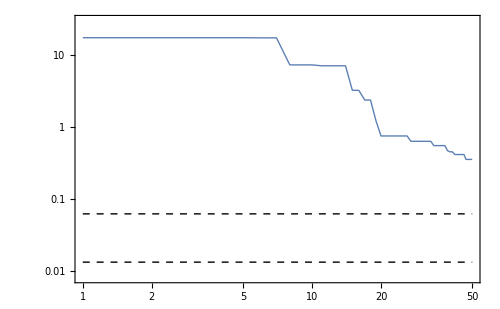

```mathematica
(* Plot of χ^2 over the generations -> We should modify the configuration of the GA *)
ListLogLogPlot[GApop⟦All,1⟧//Abs,Joined->True,
PlotRange->{{1,generations},{30,0.008}},PlotStyle->Thick,
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\chi^2"},RotateLabel->False,BaseStyle->{FontFamily->"Times",FontSize->13},ImageSize->500,
Epilog->{{Dashed,Line[{{1,0.061574},{generations,0.061574}}//Log],Line[{{1,0.0131214},{generations,0.0131214}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{BBKS}"],Scaled[{0.75,0.29}]],Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{Eisenstein-Hu}"], Scaled[{0.25, 0.11}]]}]
```

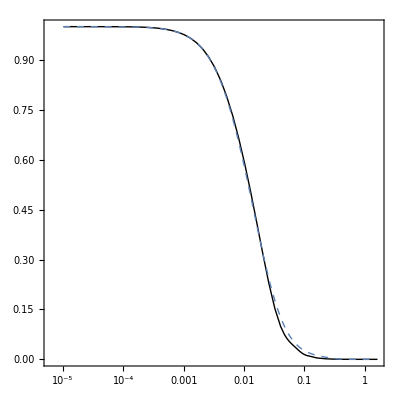

```mathematica
(* Best-Fit from the GA and the true function *)
LogLinearPlot[{GApop⟦-1,2⟧/.y->NormPartData⟦10⟧⟦1,2⟧/.z->NormPartData⟦10⟧⟦1,3⟧}//Evaluate,{x,10^-5,1.2},PlotRange->All,PlotStyle->{Directive[Dotted,Thick],Directive[Dashed]},
Frame->True,FrameStyle->BlackFrame,
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[Table[{NormPartData⟦10⟧⟦i,1⟧,NormPartData⟦10⟧⟦i,4⟧},{i,1,Length[NormPartData⟦1⟧]}],Joined->True,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T^2(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Thick,Black},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},
LegendLayout->{"Row",1},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%]
```

```mathematica
(* χ^2 for each T^2(k); there are 16 datasets *)
χ2=Table[Sum[{(NormPartData⟦j⟧⟦i,4⟧-GApop⟦-1,2⟧/.x->NormPartData⟦j⟧⟦i,1⟧/.y->NormPartData⟦j⟧⟦1,2⟧/.z->NormPartData⟦j⟧⟦1,3⟧)^2},{i,1,Length[NormPartData⟦j⟧]}],{j,1,Length[NormPartData]}]
```

{{0.0289631},{0.0116686},{0.016852},{0.0415977},{0.0263227},{0.00930604},{0.015064},{0.0406187},{0.0249},{0.00738681},{0.0130148},{0.0387419},{0.0248744},{0.00603328},{0.0107779},{0.0359995}}

### Several Random Seeds

```mathematica
(* We tray several random seeds *)
samples=10;
prog`int=0;prog`pop=0;prog`mut=0;prog`cross=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
Do[GApop1[jj]=GAevo[1234jj,generations,110,0.75,0.4,False]//Quiet;prog`pop++;prog`int=0;,{jj,1,samples}];
```

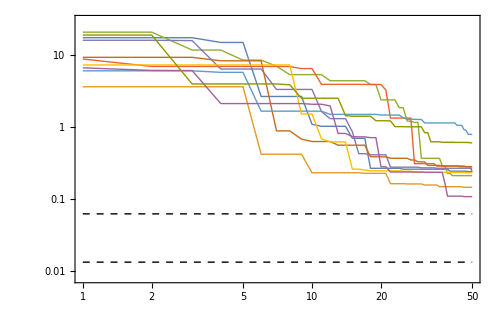

```mathematica
(* Plot the χ^2 GA solutions *)
Severalχ2=ListLogLogPlot[Table[GApop1[jj]⟦All,1⟧//Abs,{jj,1,samples}],Joined->True,PlotRange->{{1,generations},{30,0.008}},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\chi^2"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,PlotStyle->Thick,ImageSize->500,
Epilog->{{Dashed,Line[{{1,0.061574},{generations,0.061574}}//Log],Line[{{1,0.0131214},{generations,0.0131214}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{BBKS}"],Scaled[{0.75,0.2}]],Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{Eisenstein-Hu}"], Scaled[{0.25, 0.11}]]}]
```

```mathematica
(* Fitness/expression of the best individual for each random seed *)
BestFits=Table[-GApop1[i]⟦-1,1⟧,{i,samples}]
BestFunctions=Table[GApop1[i]⟦-1,2⟧,{i,samples}]
```

{0.238851,0.144256,0.209375,0.238091,0.264213,0.279668,0.780958,0.229566,0.106885,0.599148}

{(1-x-x^2 (-4.72872×10^-6 y^3.04022 z^3.038 Log[x]-0.755421 y^0.8472 z^3.03216 Log[x]^2-27.756 y^0.8472 z^3.3739 Log[x]^2-0.643965 y^0.093223 z^0.994203 Log[x]^3+4.17002 y^0.715727 z^0.269246 Log[x]^4-3.13891 y^0.416645 z^0.626706 Log[x]^5-21.9046 y^0.412488 z^3.91215 Log[x]^6+4.67481 y^1.88892 z^1.78775 Log[x]^9))^12,(1-x-x^2 (-25.3878 y^0.720286 z^2.44121+18.3122 y^3.30879 z^2.48814 Log[x]^2-3.90678 y^0.19497 z^0.399302 Log[x]^3+0.337325 y^0.143741 z^0.011793 Log[x]^4-10.5053 y^0.795697 z^0.917979 Log[x]^5+0.206952 y^2.57333 z^0.164642 Log[x]^6-24.861 y^3.03758 z^0.186641 Log[x]^8+0.000184664 y^2.48946 z^3.446 Log[x]^8))^12,(1-x-x^2 (-0.252892 y^1.64675 z^2.84982 Log[x]-1.50507 y^3.94423 z^0.239832 Log[x]^2-2.05649 y^0.0291886 z^0.0298264 Log[x]^3+0.0521523 y^0.00792171 z^0.592751 Log[x]^6+0.0000163827 y^1.91316 z^1.58147 Log[x]^7-40.6933 y^3.52365 z^1.63596 Log[x]^7-1.9904×10^-12 y^1.58731 z^3.06882 Log[x]^8-5.21561×10^-15 y^3.17518 z^2.91385 Log[x]^9))^12,(1-x-x^2 (15.9665 y^0.744591 z^0.301257 Log[x]^4+11.2644 y^0.744591 z^0.708639 Log[x]^4+2.94764 y^1.14256 z^1.05251 Log[x]^4-0.0654556 y^1.49845 z^0.700564 Log[x]^6+5.60355 y^3.49862 z^1.0675 Log[x]^8-7.10665×10^-7 y^0.191131 z^3.82145 Log[x]^8))^12,(1-x-x^2 (-4.15204 y^0.033481 z^0.249002 Log[x]^3+0.0000893812 y^1.19679 z^2.5551 Log[x]^3-258.45 y^1.47896 z^3.22402 Log[x]^3+25.7055 y^1.47896 z^0.912048 Log[x]^4+0.000179186 y^1.19679 z^2.5551 Log[x]^4-0.658555 y^0.545858 z^2.05798 Log[x]^7))^12,(1-x-x^2 (14.7687 y^1.28648 z^2.80222+13.184 y^2.7299 z^2.85938+30.4498 y^2.99388 z^3.49172-3.56256 y^0.16934 z^0.0212394 Log[x]^3-252.347 y^3.58456 z^2.11812 Log[x]^3+2.10646 y^0.028248 z^2.47291 Log[x]^6-0.000029383 y^0.349268 z^3.45479 Log[x]^7))^12,(1-x-x^2 (591.603 y^3.97282 z^0.461382 Log[x]-8.71424 y^0.928583 z^2.9908 Log[x]-0.447477 y^1.4734 z^3.35362 Log[x]^3+38.0909 y^1.20101 z^0.926811 Log[x]^4-3.12522 y^0.797557 z^0.317206 Log[x]^5-27.699 y^0.476191 z^1.84832 Log[x]^5-20.2776 y^0.671801 z^3.04386 Log[x]^6+24.6384 y^1.97832 z^3.20015 Log[x]^9))^12,(1-x-x^2 (-6.38907 y^1.06157 z^2.19125 Log[x]+1.20221×10^-6 y^0.379159 z^3.16671 Log[x]^3+2.95654 y^0.409946 z^0.436522 Log[x]^4+6.43139 y^0.475826 z^0.436522 Log[x]^4+0.0203319 y^3.28851 z^3.34367 Log[x]^4+0.0108212 y^0.261938 z^0.329454 Log[x]^5+0.70122 y^2.76807 z^0.282671 Log[x]^9))^12,(1-x-x^2 (-9.79094 y^1.33682 z^0.632905 Log[x]^2+63.7671 y^1.31125 z^0.0753415 Log[x]^4+0.00494058 y^0.65002 z^2.0983 Log[x]^4-13.2274 y^0.949914 z^0.549323 Log[x]^5-0.00658751 y^2.32119 z^0.039237 Log[x]^8+0.0690047 y^1.87409 z^0.548998 Log[x]^8-1253.12 y^2.80696 z^2.06016 Log[x]^8))^12,(1-x-x^2 (-1.96046 y^1.49061 z^1.02878-3.94522 y^1.22892 z^1.88761 Log[x]^3+168.933 y^0.345459 z^2.11648 Log[x]^4-115.976 y^1.90291 z^2.81948 Log[x]^6+0.0664642 y^3.43286 z^0.485279 Log[x]^8-2.01467×10^-10 y^3.73037 z^3.67684 Log[x]^8))^12}

```mathematica
(* Best individual for several random seeds *)
Abs[Min[BestFits]]
BestFit=Position[BestFits,Min[BestFits]]⟦1⟧⟦1⟧;
```

0.106885

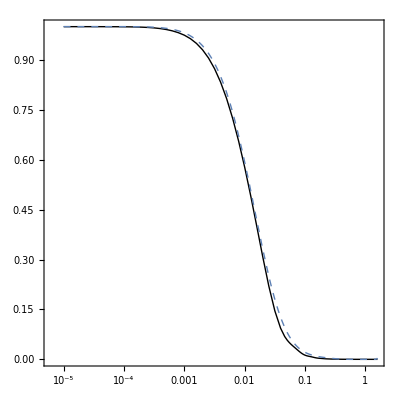

```mathematica
(* Best-Fit from the GA and the true function *)
LogLinearPlot[{GApop1[BestFit]⟦-1,2⟧/.y->NormPartData⟦5⟧⟦1,2⟧/.z->NormPartData⟦5⟧⟦1,3⟧}//Evaluate,{x,10^-5,1.6},PlotRange->All,PlotStyle->{Directive[Dotted,Thick],Directive[Dashed]},
Frame->True,FrameStyle->BlackFrame,BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[Table[{NormPartData⟦5⟧⟦i,1⟧,NormPartData⟦5⟧⟦i,4⟧},{i,1,Length[NormPartData⟦5⟧]}],Joined->True,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T^2(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Thick,Black},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},
LegendLayout->{"Row",4},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%]
```

```mathematica
(* χ^2 for the 16 datasets *)
χ2=Table[Sum[{(NormPartData⟦j⟧⟦i,4⟧-GApop1[BestFit]⟦-1,2⟧/.x->NormPartData⟦j⟧⟦i,1⟧/.y->NormPartData⟦j⟧⟦1,2⟧/.z->NormPartData⟦j⟧⟦1,3⟧)^2},{i,1,Length[NormPartData⟦j⟧]}],{j,1,Length[NormPartData]}]
```

{{0.0152312},{0.00533129},{0.00240245},{0.00566281},{0.010608},{0.00337834},{0.00277277},{0.00806104},{0.00730973},{0.00251726},{0.00401436},{0.0111292},{0.00515585},{0.00258409},{0.00598234},{0.0147446}}

## General Search

### Several Fits:

```mathematica
(* Here, we run the GA for several coonfigurations and random seeds. The jobs were executed in a workstation *)
generations=50;
(* GA parameters: {population, crossover-rate, mutation-rate} *)
GAPrmts=Table[{Pop,PCross,PMut},{Pop,50,150,10},{PCross,0.6,0.8,0.05},{PMut,0.2,0.5,0.05}];
DimsGAPrmts=Dimensions[%];
```

```mathematica
(* To store the data while running *)
SaveState={};
SetSharedVariable[SaveState];
```

```mathematica
t0=AbsoluteTime[];
ParallelDo[ (* Run for each population, crossover-rate, mutation-rate, using 10 random seeds *)
Do[
Do[
Do[GApop2[i,j,k,l]=GAevo[1234l,generations,GAPrmts⟦i,j,k⟧⟦1⟧,GAPrmts⟦i,j,k⟧⟦2⟧,GAPrmts⟦i,j,k⟧⟦3⟧,False]//Quiet;
Print["Time: ", AbsoluteTime[]-t0];
AppendTo[SaveState,{i,j,k,GApop2[i,j,k,l]⟦-1,1⟧,1234l}]; (* Save the position, χ^2, and random seed *)
Export["Save_State.txt",SaveState,"Table"];, (* Export to store when each loop is done *)
{i,1,DimsGAPrmts⟦1⟧}],
{j,1,DimsGAPrmts⟦2⟧}],
{k,1,DimsGAPrmts⟦3⟧}],
{l,1,10}]
Speak["Listo el pollo"]
```

Time: 71.859829

Time: 71.929395

Time: 72.791344

Time: 74.564956

Time: 76.243578

Time: 76.629723

Time: 80.03406

Time: 81.867762

Time: 82.451997

Time: 85.132941

Time: 144.48966

Time: 144.65937

Time: 148.05487

Time: 149.05573

Time: 153.8374

Time: 153.89057

Time: 155.59703

Time: 161.50517

Time: 162.68696

Time: 171.82088

Time: 226.29957

Time: 231.97853

Time: 232.18728

Time: 234.887

Time: 235.65102

Time: 238.90803

Time: 241.66481

Time: 258.00084

Time: 261.90377

Time: 261.95123

Time: 332.23502

Time: 338.68947

Time: 338.97861

Time: 339.81996

Time: 344.33545

Time: 346.68722

Time: 353.25064

Time: 356.553027

Time: 369.625905

Time: 378.600135

Time: 446.48691

Time: 454.983284

Time: 464.675216

Time: 465.883579

Time: 467.298616

Time: 467.729996

Time: 479.77676

Time: 482.335296

Time: 497.586406

Time: 507.177566

Time: 573.843629

Time: 585.534706

Time: 586.163382

Time: 605.020087

Time: 607.397834

Time: 611.5478

Time: 617.358704

Time: 618.439719

Time: 627.506496

Time: 646.48845

Time: 702.983259

Time: 726.448172

Time: 737.442909

Time: 752.270664

Time: 754.96593

Time: 759.699494

Time: 760.080728

Time: 761.587269

Time: 769.101293

Time: 784.634063

Time: 845.29656

Time: 882.773497

Time: 895.025799

Time: 905.307775

Time: 908.975342

Time: 911.206795

Time: 914.592234

Time: 915.411199

Time: 931.815282

Time: 942.452419

Time: 1015.85017

Time: 1059.7781

Time: 1079.48491

Time: 1084.59915

Time: 1092.80755

Time: 1094.22538

Time: 1095.60607

Time: 1098.12393

Time: 1109.1636

Time: 1130.20824

Time: 1208.04265

Time: 1243.07058

Time: 1274.30194

Time: 1278.28397

Time: 1280.99659

Time: 1285.79744

Time: 1287.60468

Time: 1290.33564

Time: 1306.28685

Time: 1311.97823

Time: 1388.46366

Time: 1438.96128

Time: 1451.04977

Time: 1473.5328

Time: 1483.88065

Time: 1484.59157

Time: 1485.11595

Time: 1489.16936

Time: 1500.79162

Time: 1506.72857

Time: 1513.73804

Time: 1518.19556

Time: 1521.12015

Time: 1541.37479

Time: 1544.91629

Time: 1546.94356

Time: 1551.76343

Time: 1560.31795

Time: 1566.64717

Time: 1580.59517

Time: 1580.94407

Time: 1582.72987

Time: 1606.32937

Time: 1611.79193

Time: 1620.01861

Time: 1620.9759

Time: 1627.31395

Time: 1628.88374

Time: 1629.79329

Time: 1656.90673

Time: 1660.96632

Time: 1664.26416

Time: 1693.10712

Time: 1697.72485

Time: 1698.16384

Time: 1699.00819

Time: 1708.54195

Time: 1710.22237

Time: 1717.20785

Time: 1738.36803

Time: 1747.39193

Time: 1777.30491

Time: 1796.93466

Time: 1806.66823

Time: 1807.56329

Time: 1816.43939

Time: 1817.93729

Time: 1818.27565

Time: 1826.58615

Time: 1843.16159

Time: 1858.63288

Time: 1892.49819

Time: 1916.21336

Time: 1920.27219

Time: 1943.3023

Time: 1944.39798

Time: 1944.78019

Time: 1951.30967

Time: 1954.73145

Time: 1975.67056

Time: 1996.55295

Time: 2027.99839

Time: 2055.44376

Time: 2060.2015

Time: 2060.54993

Time: 2073.23243

Time: 2077.80059

Time: 2081.81274

Time: 2099.18117

Time: 2112.73158

Time: 2128.49793

Time: 2176.65836

Time: 2184.9276

Time: 2204.7015

Time: 2208.01464

Time: 2212.98171

Time: 2223.25979

Time: 2238.0076

Time: 2249.95516

Time: 2252.30599

Time: 2262.81564

Time: 2332.67746

Time: 2347.92183

Time: 2363.00176

Time: 2376.30265

Time: 2382.0856

Time: 2385.02351

Time: 2389.84391

Time: 2413.10548

Time: 2420.20554

Time: 2424.23022

Time: 2503.8952

Time: 2532.58635

Time: 2542.48898

Time: 2558.16386

Time: 2572.15109

Time: 2577.36277

Time: 2586.53336

Time: 2596.32692

Time: 2602.20328

Time: 2609.90016

Time: 2697.44783

Time: 2723.17575

Time: 2724.79668

Time: 2748.94745

Time: 2763.24759

Time: 2767.5167

Time: 2769.1255

Time: 2788.38276

Time: 2789.63112

Time: 2813.71466

Time: 2826.7036

Time: 2900.16311

Time: 2904.2798

Time: 2923.16699

Time: 2924.84634

Time: 2943.76686

Time: 2961.53197

Time: 2983.5278

Time: 2986.63775

Time: 2986.77716

Time: 2990.82539

Time: 2997.18671

Time: 2997.93773

Time: 2998.37155

Time: 3023.27357

Time: 3027.60728

Time: 3037.17454

Time: 3048.31003

Time: 3051.85046

Time: 3061.94524

Time: 3066.53231

Time: 3067.3543

Time: 3075.83534

Time: 3088.30028

Time: 3099.94452

Time: 3103.37031

Time: 3105.50401

Time: 3125.58575

Time: 3134.80162

Time: 3134.94492

Time: 3144.05109

Time: 3144.78694

Time: 3169.00082

Time: 3169.91371

Time: 3194.55118

Time: 3201.92082

Time: 3202.38517

Time: 3205.7423

Time: 3224.76869

Time: 3231.89768

Time: 3235.93129

Time: 3251.92888

Time: 3259.09455

Time: 3282.6467

Time: 3299.12116

Time: 3312.08296

Time: 3328.5965

Time: 3340.98374

Time: 3342.21112

Time: 3346.56228

Time: 3349.31001

Time: 3367.19972

Time: 3392.67758

Time: 3397.84623

Time: 3412.63108

Time: 3440.42057

Time: 3463.58551

Time: 3479.58473

Time: 3481.86929

Time: 3484.98973

Time: 3490.11385

Time: 3492.0504

Time: 3539.1924

Time: 3546.058647

Time: 3555.886626

Time: 3576.89601

Time: 3597.544049

Time: 3610.496433

Time: 3621.84675

Time: 3623.249761

Time: 3636.393749

Time: 3639.690642

Time: 3682.723625

Time: 3693.41404

Time: 3703.936086

Time: 3704.811486

Time: 3754.59363

Time: 3766.233937

Time: 3774.420604

Time: 3780.220614

Time: 3798.549507

Time: 3799.798952

Time: 3854.554319

Time: 3855.099385

Time: 3879.674166

Time: 3886.486495

Time: 3925.814286

Time: 3946.945428

Time: 3960.991653

Time: 3962.252249

Time: 3989.069992

Time: 3995.236972

Time: 4036.531947

Time: 4058.331832

Time: 4071.563681

Time: 4076.586509

Time: 4106.898982

Time: 4141.266735

Time: 4146.659554

Time: 4147.754365

Time: 4176.738121

Time: 4190.092607

Time: 4236.807129

Time: 4246.52314

Time: 4252.03313

Time: 4273.16204

Time: 4283.045709

Time: 4299.360384

Time: 4317.956133

Time: 4321.566978

Time: 4348.862484

Time: 4354.784199

Time: 4370.557005

Time: 4388.424036

Time: 4409.832864

Time: 4438.591829

Time: 4440.093993

Time: 4471.685737

Time: 4490.14646

Time: 4497.580247

Time: 4501.713637

Time: 4511.717051

Time: 4514.721369

Time: 4517.941636

Time: 4529.705798

Time: 4562.467236

Time: 4565.202699

Time: 4567.069838

Time: 4570.330686

Time: 4581.543523

Time: 4593.092558

Time: 4593.461957

Time: 4596.061893

Time: 4610.60489

Time: 4624.405382

Time: 4631.711731

Time: 4634.86058

Time: 4640.337865

Time: 4640.487562

Time: 4662.615047

Time: 4665.837891

Time: 4685.763132

Time: 4685.912013

Time: 4710.350098

Time: 4715.670914

Time: 4722.488408

Time: 4733.448298

Time: 4744.769423

Time: 4747.401375

Time: 4753.010897

Time: 4759.343498

Time: 4802.173903

Time: 4802.213542

Time: 4809.051923

Time: 4809.384737

Time: 4837.684391

Time: 4839.805268

Time: 4848.156134

Time: 4867.519555

Time: 4892.048648

Time: 4892.132315

Time: 4909.454875

Time: 4931.412808

Time: 4936.9765

Time: 4950.128092

Time: 4956.528884

Time: 4970.513253

Time: 4974.834545

Time: 5006.526072

Time: 5034.762417

Time: 5064.726363

Time: 5065.038902

Time: 5086.144983

Time: 5091.407153

Time: 5094.905963

Time: 5101.645371

Time: 5108.174483

Time: 5114.901846

Time: 5154.108468

Time: 5184.021284

Time: 5212.00474

Time: 5226.085859

Time: 5242.628149

Time: 5255.776959

Time: 5257.009807

Time: 5270.751532

Time: 5284.106569

Time: 5285.803327

Time: 5302.172179

Time: 5344.330395

Time: 5362.475815

Time: 5419.272589

Time: 5422.016691

Time: 5433.805857

Time: 5435.001564

Time: 5450.565546

Time: 5471.283429

Time: 5478.821286

Time: 5499.102873

Time: 5522.728129

Time: 5535.073989

Time: 5600.786522

Time: 5610.545067

Time: 5631.512849

Time: 5644.035592

Time: 5645.873842

Time: 5674.367004

Time: 5681.644113

Time: 5691.425752

Time: 5719.725886

Time: 5735.44736

Time: 5793.661722

Time: 5805.638096

Time: 5821.302127

Time: 5841.519466

Time: 5860.679542

Time: 5863.044793

Time: 5876.750511

Time: 5880.451369

Time: 5894.413881

Time: 5896.393655

Time: 5918.968893

Time: 5942.911684

Time: 5964.421007

Time: 5977.172177

Time: 6040.654503

Time: 6047.023851

Time: 6070.297063

Time: 6090.451651

Time: 6099.89063

Time: 6100.299215

Time: 6115.760409

Time: 6117.217293

Time: 6136.937984

Time: 6155.770261

Time: 6156.522027

Time: 6162.941409

Time: 6163.620628

Time: 6181.626657

Time: 6183.950841

Time: 6192.551503

Time: 6223.94242

Time: 6225.669814

Time: 6229.638297

Time: 6234.79577

Time: 6238.831966

Time: 6256.551953

Time: 6272.265207

Time: 6272.932281

Time: 6275.132561

Time: 6297.536804

Time: 6314.182049

Time: 6317.012484

Time: 6322.622544

Time: 6331.359368

Time: 6357.852871

Time: 6358.174478

Time: 6359.791018

Time: 6366.217954

Time: 6374.811797

Time: 6388.23233

Time: 6399.014533

Time: 6429.096707

Time: 6448.078897

Time: 6459.178782

Time: 6459.921963

Time: 6469.605943

Time: 6470.368706

Time: 6471.288183

Time: 6509.801804

Time: 6517.74763

Time: 6522.715396

Time: 6554.426989

Time: 6555.085784

Time: 6594.67254

Time: 6603.683575

Time: 6607.896254

Time: 6608.429233

Time: 6610.797134

Time: 6639.320211

Time: 6653.298517

Time: 6674.170818

Time: 6674.287564

Time: 6701.966963

Time: 6740.762457

Time: 6741.880162

Time: 6745.421224

Time: 6769.619241

Time: 6779.00077

Time: 6784.742974

Time: 6796.860148

Time: 6820.996427

Time: 6871.892229

Time: 6880.510256

Time: 6900.452766

Time: 6905.331185

Time: 6912.20553

Time: 6921.341611

Time: 6935.783218

Time: 6955.576869

Time: 6977.340131

Time: 6980.26981

Time: 7065.911393

Time: 7087.270959

Time: 7090.603865

Time: 7092.961905

Time: 7096.039239

Time: 7116.001226

Time: 7120.931837

Time: 7142.839041

Time: 7150.964751

Time: 7187.799498

Time: 7285.218728

Time: 7290.653281

Time: 7306.097603

Time: 7307.462659

Time: 7307.559446

Time: 7314.907849

Time: 7315.754155

Time: 7325.724712

Time: 7338.682635

Time: 7368.907184

Time: 7400.586463

Time: 7430.649475

Time: 7458.381909

Time: 7498.268655

Time: 7504.769179

Time: 7511.303452

Time: 7516.077752

Time: 7525.718664

Time: 7536.098524

Time: 7539.966657

Time: 7547.775409

Time: 7550.060521

Time: 7555.200264

Time: 7588.641417

Time: 7619.822974

Time: 7712.507108

Time: 7724.783794

Time: 7734.172349

Time: 7736.362048

Time: 7736.832767

Time: 7758.448707

Time: 7776.758534

Time: 7786.570016

Time: 7787.036288

Time: 7788.007592

Time: 7791.428804

Time: 7806.028252

Time: 7807.634555

Time: 7822.515245

Time: 7838.035108

Time: 7840.962395

Time: 7847.295121

Time: 7850.59002

Time: 7853.662301

Time: 7855.965065

Time: 7865.950882

Time: 7879.555307

Time: 7897.883414

Time: 7920.959599

Time: 7925.60463

Time: 7930.855862

Time: 7937.860033

Time: 7944.000332

Time: 7963.676871

Time: 7971.38801

Time: 7985.306971

Time: 7986.542958

Time: 8011.212096

Time: 8013.947649

Time: 8016.772583

Time: 8019.993234

Time: 8024.019289

Time: 8034.514888

Time: 8062.660703

Time: 8082.359325

Time: 8089.379173

Time: 8102.745828

Time: 8104.118101

Time: 8126.934692

Time: 8128.376506

Time: 8129.187276

Time: 8135.909348

Time: 8149.967733

Time: 8159.040591

Time: 8186.710332

Time: 8187.166502

Time: 8202.526851

Time: 8243.3644

Time: 8243.510981

Time: 8247.688826

Time: 8257.360016

Time: 8259.603296

Time: 8280.532129

Time: 8311.378725

Time: 8315.952357

Time: 8322.04921

Time: 8339.602303

Time: 8354.109489

Time: 8376.15398

Time: 8382.321027

Time: 8395.697778

Time: 8423.511514

Time: 8429.297451

Time: 8441.79173

Time: 8453.293759

Time: 8476.925223

Time: 8485.692476

Time: 8511.642263

Time: 8520.401985

Time: 8531.16136

Time: 8558.054699

Time: 8585.534327

Time: 8586.303051

Time: 8601.087498

Time: 8602.007878

Time: 8614.642289

Time: 8650.599317

Time: 8680.635193

Time: 8691.560291

Time: 8707.24566

Time: 8724.33302

Time: 8737.879037

Time: 8749.619749

Time: 8754.540824

Time: 8769.0172

Time: 8795.288306

Time: 8813.262388

Time: 8814.164078

Time: 8832.305292

Time: 8869.528935

Time: 8872.894426

Time: 8877.675958

Time: 8892.251292

Time: 8899.239464

Time: 8913.874511

Time: 8934.05868

Time: 8950.797853

Time: 8953.828779

Time: 8990.743862

Time: 8997.536127

Time: 9034.03689

Time: 9040.581067

Time: 9059.811629

Time: 9068.902055

Time: 9076.804646

Time: 9093.488247

Time: 9123.089312

Time: 9126.986391

Time: 9137.207152

Time: 9146.394992

Time: 9158.061426

Time: 9194.236198

Time: 9194.553229

Time: 9217.946375

Time: 9218.273372

Time: 9233.769212

Time: 9243.361008

Time: 9255.827162

Time: 9258.827875

Time: 9259.080563

Time: 9260.818748

Time: 9265.305354

Time: 9282.330046

Time: 9292.477813

Time: 9297.149246

Time: 9311.455486

Time: 9327.691092

Time: 9333.596987

Time: 9336.057557

Time: 9350.478227

Time: 9373.010191

Time: 9383.761107

Time: 9383.941452

Time: 9385.040979

Time: 9392.789427

Time: 9398.630739

Time: 9423.82232

Time: 9429.751864

Time: 9443.684955

Time: 9456.962437

Time: 9472.79949

Time: 9473.845258

Time: 9475.996567

Time: 9513.419776

Time: 9514.02907

Time: 9529.963546

Time: 9530.42057

Time: 9532.4724

Time: 9533.250685

Time: 9565.673968

Time: 9567.671842

Time: 9576.87168

Time: 9603.630594

Time: 9608.875081

Time: 9622.897528

Time: 9659.916483

Time: 9673.195283

Time: 9684.275732

Time: 9690.76049

Time: 9695.048957

Time: 9697.642987

Time: 9708.93979

Time: 9709.731305

Time: 9735.681488

Time: 9751.41748

Time: 9793.105974

Time: 9800.704828

Time: 9805.787808

Time: 9815.998317

Time: 9825.063727

Time: 9852.39099

Time: 9873.197696

Time: 9887.601881

Time: 9899.876982

Time: 9904.760266

Time: 9916.453303

Time: 9929.405276

Time: 9956.380018

Time: 9964.263608

Time: 9969.753927

Time: 10020.79541

Time: 10025.6073

Time: 10036.18054

Time: 10068.83126

Time: 10080.18911

Time: 10089.16702

Time: 10101.2371

Time: 10125.87836

Time: 10138.48351

Time: 10143.54169

Time: 10156.18174

Time: 10177.48409

Time: 10179.33069

Time: 10210.91057

Time: 10234.87762

Time: 10260.432

Time: 10280.37014

Time: 10287.4041

Time: 10310.98953

Time: 10315.0914

Time: 10327.86446

Time: 10335.42493

Time: 10338.67583

Time: 10339.73449

Time: 10358.99062

Time: 10395.26521

Time: 10409.75281

Time: 10412.13464

Time: 10460.91339

Time: 10475.5599

Time: 10498.78595

Time: 10517.99948

Time: 10520.03923

Time: 10530.07423

Time: 10530.57688

Time: 10546.73926

Time: 10560.93297

Time: 10599.48482

Time: 10599.56559

Time: 10614.72443

Time: 10645.88534

Time: 10653.96798

Time: 10658.28143

Time: 10676.93897

Time: 10682.59107

Time: 10707.05212

Time: 10717.82467

Time: 10724.72329

Time: 10727.87096

Time: 10728.00235

Time: 10729.91461

Time: 10759.34501

Time: 10762.32777

Time: 10771.83131

Time: 10788.4648

Time: 10793.88665

Time: 10794.22843

Time: 10800.10386

Time: 10804.93046

Time: 10830.29476

Time: 10836.1371

Time: 10845.44005

Time: 10859.13422

Time: 10866.73627

Time: 10876.96714

Time: 10884.83648

Time: 10910.87962

Time: 10918.12979

Time: 10924.93081

Time: 10938.86383

Time: 10944.41028

Time: 10953.68269

Time: 10970.27533

Time: 10976.11066

Time: 10993.62353

Time: 11000.91594

Time: 11004.18689

Time: 11006.17818

Time: 11023.08946

Time: 11052.94654

Time: 11058.18052

Time: 11071.97153

Time: 11084.7389

Time: 11084.75019

Time: 11099.28806

Time: 11132.97336

Time: 11147.69124

Time: 11148.21894

Time: 11150.67043

Time: 11180.46458

Time: 11187.87104

Time: 11190.51492

Time: 11195.79137

Time: 11226.2777

Time: 11226.31737

Time: 11288.62475

Time: 11295.46416

Time: 11304.5385

Time: 11317.82503

Time: 11321.37436

Time: 11332.23982

Time: 11335.17133

Time: 11350.47663

Time: 11370.16934

Time: 11377.20199

Time: 11417.97187

Time: 11449.50877

Time: 11456.17674

Time: 11474.20964

Time: 11478.46408

Time: 11499.23255

Time: 11501.91374

Time: 11526.5378

Time: 11537.49141

Time: 11542.79431

Time: 11550.87686

Time: 11595.30548

Time: 11634.72325

Time: 11642.53304

Time: 11645.80925

Time: 11661.78685

Time: 11662.87898

Time: 11690.25831

Time: 11690.99547

Time: 11711.40481

Time: 11718.55397

Time: 11727.78742

Time: 11732.03994

Time: 11745.67132

Time: 11824.19833

Time: 11826.47461

Time: 11828.47185

Time: 11839.59597

Time: 11848.80441

Time: 11855.62497

Time: 11881.19929

Time: 11903.42857

Time: 11905.73512

Time: 11912.1595

Time: 11913.97403

Time: 11958.42325

Time: 12015.36103

Time: 12023.03608

Time: 12044.24325

Time: 12060.43039

Time: 12060.54769

Time: 12072.99058

Time: 12098.9333

Time: 12115.64031

Time: 12118.61658

Time: 12123.62413

Time: 12129.76341

Time: 12172.50856

Time: 12189.75057

Time: 12191.88543

Time: 12196.1119

Time: 12224.29668

Time: 12249.56956

Time: 12252.36258

Time: 12266.09792

Time: 12270.15923

Time: 12281.07146

Time: 12281.36754

Time: 12289.24031

Time: 12293.25516

Time: 12297.61918

Time: 12317.72036

Time: 12328.45092

Time: 12353.64664

Time: 12360.7957

Time: 12362.28726

Time: 12375.13589

Time: 12377.77943

Time: 12381.98923

Time: 12392.30387

Time: 12392.61328

Time: 12425.19469

Time: 12443.87845

Time: 12459.65812

Time: 12459.9739

Time: 12467.01405

Time: 12492.48118

Time: 12497.74374

Time: 12497.89209

Time: 12527.03928

Time: 12527.71831

Time: 12554.88754

Time: 12575.0692

Time: 12576.38533

Time: 12577.68599

Time: 12589.25518

Time: 12596.74855

Time: 12606.06394

Time: 12624.50455

Time: 12640.79927

Time: 12666.92517

Time: 12673.57345

Time: 12685.43516

Time: 12714.63976

Time: 12728.0276

Time: 12745.11214

Time: 12761.71525

Time: 12767.80427

Time: 12774.08115

Time: 12788.50925

Time: 12791.45542

Time: 12829.1135

Time: 12836.3184

Time: 12868.23975

Time: 12875.63723

Time: 12880.64648

Time: 12899.73997

Time: 12903.98023

Time: 12948.93444

Time: 12974.90097

Time: 12981.98648

Time: 12991.66221

Time: 12999.39051

Time: 13002.61482

Time: 13034.33222

Time: 13051.96994

Time: 13057.04798

Time: 13072.51769

Time: 13091.4304

Time: 13126.92582

Time: 13133.9667

Time: 13135.7214

Time: 13136.73236

Time: 13199.33619

Time: 13206.36537

Time: 13219.10141

Time: 13236.07899

Time: 13237.77127

Time: 13258.51172

Time: 13264.61559

Time: 13283.90392

Time: 13293.39316

Time: 13318.29847

Time: 13326.27042

Time: 13337.55803

Time: 13350.63203

Time: 13400.53123

Time: 13427.51411

Time: 13431.1472

Time: 13438.96885

Time: 13469.52562

Time: 13474.73488

Time: 13477.68753

Time: 13485.22059

Time: 13520.19072

Time: 13524.30048

Time: 13551.73091

Time: 13592.96788

Time: 13625.19167

Time: 13646.69236

Time: 13649.22865

Time: 13674.10922

Time: 13689.88287

Time: 13691.73337

Time: 13692.55856

Time: 13708.1551

Time: 13718.30802

Time: 13749.02974

Time: 13755.57318

Time: 13771.71462

Time: 13783.41876

Time: 13812.29839

Time: 13844.92581

Time: 13869.78909

Time: 13874.96655

Time: 13881.5901

Time: 13885.11481

Time: 13887.73976

Time: 13893.41768

Time: 13917.20189

Time: 13934.5092

Time: 13949.78841

Time: 13951.20649

Time: 13956.98271

Time: 13957.09955

Time: 13982.53639

Time: 13983.9832

Time: 13989.12159

Time: 14007.88088

Time: 14033.41505

Time: 14035.43154

Time: 14046.47696

Time: 14063.44358

Time: 14071.29336

Time: 14102.03729

Time: 14114.46086

Time: 14126.44874

Time: 14127.17862

Time: 14137.1298

Time: 14143.92926

Time: 14145.4634

Time: 14154.32615

Time: 14186.976

Time: 14207.51266

Time: 14210.4492

Time: 14220.05078

Time: 14237.37112

Time: 14241.80223

Time: 14259.10086

Time: 14274.73746

Time: 14280.7565

Time: 14289.93267

Time: 14316.10597

Time: 14339.57854

Time: 14368.58156

Time: 14375.31005

Time: 14379.61844

Time: 14389.83504

Time: 14400.1449

Time: 14411.61605

Time: 14420.94439

Time: 14435.60521

Time: 14467.15138

Time: 14511.54402

Time: 14517.05622

Time: 14519.44964

Time: 14540.31761

Time: 14548.56752

Time: 14559.40359

Time: 14563.10938

Time: 14583.83601

Time: 14601.73724

Time: 14608.64754

Time: 14628.3507

Time: 14657.95651

Time: 14669.29686

Time: 14696.48337

Time: 14709.79851

Time: 14719.66884

Time: 14721.5217

Time: 14725.64945

Time: 14754.63413

Time: 14779.37389

Time: 14797.74502

Time: 14809.01161

Time: 14823.37311

Time: 14855.37827

Time: 14862.33803

Time: 14873.27642

Time: 14892.90301

Time: 14904.92798

Time: 14918.82331

Time: 14925.47373

Time: 14928.01865

Time: 14969.42124

Time: 14969.6446

Time: 14975.32846

Time: 15006.69155

Time: 15026.41328

Time: 15089.88988

Time: 15095.63706

Time: 15107.74525

Time: 15108.10775

Time: 15112.12253

Time: 15134.0196

Time: 15153.5691

Time: 15156.44484

Time: 15162.1753

Time: 15219.05756

Time: 15244.98318

Time: 15247.67493

Time: 15311.9618

Time: 15319.42898

Time: 15322.21287

Time: 15336.81286

Time: 15338.01118

Time: 15359.22104

Time: 15369.83332

Time: 15376.93942

Time: 15381.00987

Time: 15386.36298

Time: 15395.09946

Time: 15404.23237

Time: 15444.86268

Time: 15466.32114

Time: 15469.25656

Time: 15487.87554

Time: 15517.65092

Time: 15542.32041

Time: 15551.31814

Time: 15562.83634

Time: 15571.53367

Time: 15587.35336

Time: 15589.60825

Time: 15595.69212

Time: 15595.85469

Time: 15602.39947

Time: 15627.53461

Time: 15639.79245

Time: 15646.74006

Time: 15648.30757

Time: 15656.89927

Time: 15672.56941

Time: 15683.50738

Time: 15688.75429

Time: 15689.63828

Time: 15712.30259

Time: 15725.3067

Time: 15766.38554

Time: 15771.5558

Time: 15774.08551

Time: 15782.28984

Time: 15791.02829

Time: 15804.54661

Time: 15808.95871

Time: 15816.56779

Time: 15831.77957

Time: 15834.93016

Time: 15860.77724

Time: 15881.47514

Time: 15896.35382

Time: 15898.19035

Time: 15900.35979

Time: 15920.90566

Time: 15939.55612

Time: 15940.68059

Time: 15969.87503

Time: 15974.81451

Time: 15979.93803

Time: 16002.08063

Time: 16003.73584

Time: 16026.75312

Time: 16030.22275

Time: 16039.13637

Time: 16046.77815

Time: 16061.69131

Time: 16079.36709

Time: 16095.99358

Time: 16097.53783

Time: 16108.00441

Time: 16129.68211

Time: 16167.13985

Time: 16173.52501

Time: 16179.81589

Time: 16185.50797

Time: 16194.19497

Time: 16216.47248

Time: 16229.3324

Time: 16235.38499

Time: 16237.20178

Time: 16271.79363

Time: 16282.2405

Time: 16294.19084

Time: 16295.12287

Time: 16296.67544

Time: 16311.58759

Time: 16325.1234

Time: 16380.37601

Time: 16389.59194

Time: 16392.06121

Time: 16413.02469

Time: 16418.10477

Time: 16422.37846

Time: 16443.31558

Time: 16451.31077

Time: 16476.09135

Time: 16482.35003

Time: 16487.73592

Time: 16547.64157

Time: 16558.73739

Time: 16571.48046

Time: 16577.62585

Time: 16603.59761

Time: 16607.22207

Time: 16627.8897

Time: 16640.05836

Time: 16653.20511

Time: 16654.06763

Time: 16709.6368

Time: 16714.80066

Time: 16719.22565

Time: 16738.62564

Time: 16740.39586

Time: 16787.32213

Time: 16788.5338

Time: 16822.02178

Time: 16830.39371

Time: 16840.56093

Time: 16847.42864

Time: 16851.07887

Time: 16876.86744

Time: 16878.09893

Time: 16881.01995

Time: 16884.38711

Time: 16900.07237

Time: 16922.5953

Time: 16923.67223

Time: 16943.66412

Time: 16978.02896

Time: 17013.87036

Time: 17016.47782

Time: 17039.54128

Time: 17040.42957

Time: 17043.31012

Time: 17047.50766

Time: 17062.0667

Time: 17092.37764

Time: 17097.99251

Time: 17107.62375

Time: 17110.65106

Time: 17113.51884

Time: 17122.28625

Time: 17127.00193

Time: 17134.36591

Time: 17167.61611

Time: 17183.34817

Time: 17184.40492

Time: 17193.83137

Time: 17202.52167

Time: 17231.16498

Time: 17246.68202

Time: 17249.41086

Time: 17264.62236

Time: 17265.23929

Time: 17269.50731

Time: 17271.70956

Time: 17274.80855

Time: 17327.72996

Time: 17340.27758

Time: 17372.31575

Time: 17375.45774

Time: 17375.94054

Time: 17382.89957

Time: 17383.32873

Time: 17384.95938

Time: 17390.11212

Time: 17401.68159

Time: 17439.88062

Time: 17456.83936

Time: 17468.90918

Time: 17485.44042

Time: 17507.19496

Time: 17514.73462

Time: 17519.89554

Time: 17531.49917

Time: 17532.11845

Time: 17535.84436

Time: 17540.36785

Time: 17574.88079

Time: 17580.5827

Time: 17592.55684

Time: 17616.1525

Time: 17644.55976

Time: 17645.75502

Time: 17652.88585

Time: 17665.99561

Time: 17687.0499

Time: 17705.93509

Time: 17706.32291

Time: 17715.1347

Time: 17717.1694

Time: 17718.85108

Time: 17760.68443

Time: 17776.84372

Time: 17791.40112

Time: 17799.8928

Time: 17801.90244

Time: 17816.91817

Time: 17870.9279

Time: 17879.43046

Time: 17886.03864

Time: 17891.91993

Time: 17905.38783

Time: 17910.78137

Time: 17915.50614

Time: 17916.41683

Time: 17975.29845

Time: 17986.74193

Time: 18023.20932

Time: 18045.36516

Time: 18050.1106

Time: 18069.28288

Time: 18084.13868

Time: 18098.1355

Time: 18098.57692

Time: 18110.24118

Time: 18155.2109

Time: 18166.23992

Time: 18168.95391

Time: 18190.57063

Time: 18190.90045

Time: 18225.67512

Time: 18237.2431

Time: 18249.71236

Time: 18284.05613

Time: 18303.98634

Time: 18304.7161

Time: 18306.00489

Time: 18332.24581

Time: 18351.87229

Time: 18353.72979

Time: 18364.512

Time: 18364.58583

Time: 18396.06249

Time: 18426.73825

Time: 18432.18724

Time: 18433.25149

Time: 18433.52615

Time: 18439.17115

Time: 18455.4

Time: 18504.45431

Time: 18509.44197

Time: 18517.46221

Time: 18559.87483

Time: 18560.42028

Time: 18563.24461

Time: 18582.06336

Time: 18590.45178

Time: 18616.3504

Time: 18618.03618

Time: 18627.84966

Time: 18645.31752

Time: 18647.76046

Time: 18651.17408

Time: 18667.96653

Time: 18671.80589

Time: 18685.92885

Time: 18706.27212

Time: 18730.70919

Time: 18748.0433

Time: 18753.17438

Time: 18754.25458

Time: 18757.55094

Time: 18779.69712

Time: 18781.72894

Time: 18811.62135

Time: 18838.81683

Time: 18844.07358

Time: 18847.96774

Time: 18856.93962

Time: 18872.58942

Time: 18885.57519

Time: 18897.57381

Time: 18903.25454

Time: 18906.1314

Time: 18918.43598

Time: 18952.63381

Time: 18971.32531

Time: 18996.06654

Time: 19006.71731

Time: 19009.13072

Time: 19014.81547

Time: 19022.76677

Time: 19032.52829

Time: 19038.27123

Time: 19038.47956

Time: 19042.84477

Time: 19077.10048

Time: 19082.73811

Time: 19100.34166

Time: 19126.85913

Time: 19137.4443

Time: 19144.05353

Time: 19157.53333

Time: 19180.59301

Time: 19187.35198

Time: 19214.58973

Time: 19215.12372

Time: 19218.81384

Time: 19219.96446

Time: 19222.55268

Time: 19269.11911

Time: 19272.29918

Time: 19282.32208

Time: 19299.84265

Time: 19311.33973

Time: 19313.109

Time: 19372.35223

Time: 19379.29819

Time: 19408.8426

Time: 19413.69667

Time: 19415.22961

Time: 19437.50118

Time: 19442.11823

Time: 19444.36115

Time: 19465.48598

Time: 19485.23685

Time: 19516.81745

Time: 19553.02638

Time: 19594.11407

Time: 19600.30748

Time: 19604.40857

Time: 19610.36968

Time: 19612.08799

Time: 19634.16549

Time: 19661.71006

Time: 19662.21748

Time: 19678.40269

Time: 19696.90423

Time: 19753.98042

Time: 19755.63361

Time: 19756.58775

Time: 19760.66275

Time: 19811.86507

Time: 19816.70346

Time: 19818.83314

Time: 19835.20391

Time: 19838.3288

Time: 19865.67489

Time: 19878.03392

Time: 19880.41087

Time: 19901.2484

Time: 19916.88166

Time: 19950.08041

Time: 19950.13057

Time: 19954.25083

Time: 19959.37373

Time: 19961.1315

Time: 19978.01126

Time: 20044.74749

Time: 20048.0599

Time: 20062.99711

Time: 20070.05924

Time: 20101.69239

Time: 20106.01924

Time: 20110.10135

Time: 20139.41364

Time: 20152.31657

Time: 20160.85442

Time: 20167.66892

Time: 20171.5216

Time: 20183.56724

Time: 20184.81348

Time: 20221.21865

Time: 20232.10369

Time: 20252.96546

Time: 20264.44281

Time: 20292.17271

Time: 20297.64811

Time: 20301.11584

Time: 20308.05941

Time: 20335.15269

Time: 20335.58159

Time: 20359.28547

Time: 20365.61359

Time: 20371.03557

Time: 20402.82308

Time: 20411.78835

Time: 20415.1748

Time: 20438.99557

Time: 20445.21297

Time: 20447.54987

Time: 20455.76214

Time: 20456.01101

Time: 20457.61649

Time: 20527.51237

Time: 20539.91923

Time: 20556.72927

Time: 20561.4114

Time: 20572.19685

Time: 20574.03841

Time: 20597.6799

Time: 20602.66843

Time: 20603.07608

Time: 20616.69578

Time: 20624.91969

Time: 20626.94257

Time: 20662.45994

Time: 20679.51386

Time: 20702.10299

Time: 20704.42609

Time: 20708.88725

Time: 20750.46512

Time: 20751.97382

Time: 20759.09487

Time: 20760.03911

Time: 20775.80835

Time: 20784.50632

Time: 20799.58915

Time: 20805.30518

Time: 20855.96988

Time: 20856.45939

Time: 20870.19754

Time: 20881.6487

Time: 20899.868

Time: 20908.00494

Time: 20954.45581

Time: 20975.49513

Time: 20976.36115

Time: 20982.44794

Time: 20989.1402

Time: 20998.19366

Time: 21036.14209

Time: 21049.76082

Time: 21053.22491

Time: 21077.4128

Time: 21110.82406

Time: 21120.24952

Time: 21165.96632

Time: 21186.06036

Time: 21186.13802

Time: 21186.28284

Time: 21203.41295

Time: 21206.57738

Time: 21250.54631

Time: 21259.45781

Time: 21270.88252

Time: 21283.5162

Time: 21301.21637

Time: 21339.86437

Time: 21342.66591

Time: 21367.54307

Time: 21381.34591

Time: 21391.05036

Time: 21419.86241

Time: 21440.06541

Time: 21448.85198

Time: 21452.88376

Time: 21479.26245

Time: 21496.481

Time: 21501.05319

Time: 21526.10483

Time: 21539.86907

Time: 21548.9286

Time: 21551.21636

Time: 21557.75571

Time: 21592.5323

Time: 21599.93397

Time: 21604.02757

Time: 21640.66974

Time: 21691.29571

Time: 21701.9911

Time: 21713.31215

Time: 21714.70432

Time: 21717.2204

Time: 21731.18595

Time: 21757.15059

Time: 21774.6925

Time: 21790.45032

Time: 21790.84184

Time: 21806.1179

Time: 21806.87182

Time: 21827.81389

Time: 21839.61049

Time: 21863.25077

Time: 21870.92004

Time: 21887.74862

Time: 21913.76873

Time: 21939.31147

Time: 21952.63754

Time: 21962.81531

Time: 21968.55231

Time: 21972.13882

Time: 21995.7296

Time: 22001.20031

Time: 22005.87618

Time: 22011.88928

Time: 22013.75912

Time: 22018.47974

Time: 22067.92324

Time: 22082.03606

Time: 22082.18617

Time: 22087.47116

Time: 22092.1011

Time: 22103.16781

Time: 22167.29441

Time: 22169.29375

Time: 22178.14267

Time: 22188.59034

Time: 22196.22804

Time: 22211.31061

Time: 22216.68998

Time: 22221.42039

Time: 22230.47966

Time: 22258.78121

Time: 22260.71162

Time: 22262.65649

Time: 22287.35095

Time: 22318.82276

Time: 22338.05417

Time: 22351.00088

Time: 22351.97141

Time: 22355.42392

Time: 22364.43156

Time: 22376.59213

Time: 22388.50384

Time: 22388.97872

Time: 22428.49906

Time: 22446.35673

Time: 22453.36323

Time: 22453.38026

Time: 22506.32715

Time: 22523.6517

Time: 22531.10535

Time: 22533.12738

Time: 22547.71665

Time: 22554.836

Time: 22557.88289

Time: 22608.94066

Time: 22613.56067

Time: 22653.61337

Time: 22657.57311

Time: 22658.76253

Time: 22672.61587

Time: 22681.55597

Time: 22716.61392

Time: 22753.7236

Time: 22775.62615

Time: 22781.84107

Time: 22790.4586

Time: 22791.86692

Time: 22843.33911

Time: 22844.87954

Time: 22872.71835

Time: 22876.08428

Time: 22894.85981

Time: 22913.84306

Time: 22930.88622

Time: 22943.60035

Time: 22964.08726

Time: 22970.12129

Time: 22983.47005

Time: 23017.96178

Time: 23035.99232

Time: 23049.73897

Time: 23076.91266

Time: 23080.94773

Time: 23089.46383

Time: 23101.88083

Time: 23103.93279

Time: 23127.90551

Time: 23138.36746

Time: 23150.37304

Time: 23167.22213

Time: 23178.91797

Time: 23205.97351

Time: 23226.35208

Time: 23251.34927

Time: 23253.92529

Time: 23271.56895

Time: 23284.94439

Time: 23286.56361

Time: 23308.76317

Time: 23333.56409

Time: 23344.23007

Time: 23344.97028

Time: 23376.70895

Time: 23398.13272

Time: 23418.22882

Time: 23442.73352

Time: 23446.00606

Time: 23450.94761

Time: 23475.84907

Time: 23480.96506

Time: 23489.39621

Time: 23497.32006

Time: 23513.36272

Time: 23535.60396

Time: 23548.08652

Time: 23575.82644

Time: 23576.55853

Time: 23580.21668

Time: 23598.64861

Time: 23604.42893

Time: 23621.10381

Time: 23677.18197

Time: 23680.80667

Time: 23690.11522

Time: 23691.21004

Time: 23695.24617

Time: 23707.46367

Time: 23712.32095

Time: 23716.74645

Time: 23719.45939

Time: 23732.32513

Time: 23749.49789

Time: 23759.42499

Time: 23759.94679

Time: 23775.03484

Time: 23790.89304

Time: 23804.65643

Time: 23812.96256

Time: 23825.33876

Time: 23840.82969

Time: 23842.23154

Time: 23859.38329

Time: 23873.38421

Time: 23874.91651

Time: 23896.66174

Time: 23903.7327

Time: 23911.393

Time: 23926.56016

Time: 23931.81726

Time: 23941.52902

Time: 23953.85739

Time: 23969.34365

Time: 24003.18377

Time: 24005.5585

Time: 24027.60212

Time: 24027.61049

Time: 24060.97476

Time: 24075.05765

Time: 24081.42933

Time: 24084.44244

Time: 24085.26966

Time: 24089.99388

Time: 24119.71033

Time: 24134.72484

Time: 24140.34544

Time: 24194.16896

Time: 24197.95715

Time: 24209.50062

Time: 24232.88534

Time: 24258.11882

Time: 24260.82949

Time: 24261.0406

Time: 24275.54712

Time: 24281.33267

Time: 24289.52392

Time: 24334.38759

Time: 24353.64972

Time: 24366.39546

Time: 24383.06962

Time: 24411.14527

Time: 24413.79087

Time: 24419.42204

Time: 24430.27562

Time: 24450.9497

Time: 24458.55634

Time: 24482.23993

Time: 24490.1534

Time: 24517.97482

Time: 24548.14703

Time: 24549.2551

Time: 24563.54514

Time: 24574.35404

Time: 24596.71906

Time: 24613.17067

Time: 24617.97297

Time: 24626.79523

Time: 24640.51411

Time: 24645.69953

Time: 24651.49703

Time: 24690.17249

Time: 24699.80735

Time: 24750.37496

Time: 24753.41304

Time: 24754.41729

Time: 24763.3132

Time: 24766.3923

Time: 24804.74506

Time: 24808.19546

Time: 24833.45872

Time: 24845.67687

Time: 24852.54561

Time: 24862.9249

Time: 24887.88808

Time: 24910.76839

Time: 24941.30184

Time: 24956.49623

Time: 24961.26125

Time: 24972.26024

Time: 24975.82026

Time: 24982.57789

Time: 24986.36397

Time: 25023.20532

Time: 25042.07717

Time: 25050.67598

Time: 25063.75917

Time: 25070.50455

Time: 25075.16449

Time: 25094.18209

Time: 25128.41957

Time: 25129.13328

Time: 25167.4226

Time: 25174.29328

Time: 25175.06313

Time: 25185.01256

Time: 25204.41199

Time: 25205.15155

Time: 25215.65656

Time: 25218.99503

Time: 25222.41173

Time: 25226.10633

Time: 25231.21473

Time: 25234.14249

Time: 25255.87821

Time: 25289.91938

Time: 25296.41894

Time: 25300.04673

Time: 25303.69492

Time: 25311.16666

Time: 25322.83074

Time: 25340.28959

Time: 25366.50531

Time: 25375.24596

Time: 25394.65749

Time: 25398.23236

Time: 25398.30619

Time: 25405.78694

Time: 25406.98668

Time: 25431.86715

Time: 25445.13781

Time: 25451.21151

Time: 25458.07907

Time: 25487.57903

Time: 25508.07546

Time: 25538.73762

Time: 25543.42256

Time: 25543.94145

Time: 25553.77027

Time: 25565.05725

Time: 25582.01017

Time: 25593.95828

Time: 25596.80287

Time: 25599.01518

Time: 25641.09251

Time: 25655.23577

Time: 25674.93833

Time: 25697.48373

Time: 25729.53769

Time: 25738.69337

Time: 25740.44155

Time: 25751.14977

Time: 25759.55951

Time: 25776.64618

Time: 25791.3009

Time: 25793.38546

Time: 25829.90707

Time: 25830.73933

Time: 25832.2962

Time: 25892.79683

Time: 25912.57233

Time: 25918.61887

Time: 25920.90669

Time: 25927.50094

Time: 25947.74627

Time: 25960.2567

Time: 25976.23777

Time: 26001.11931

Time: 26009.17339

Time: 26019.42318

Time: 26040.58291

Time: 26086.38122

Time: 26096.95962

Time: 26098.85806

Time: 26122.01191

Time: 26135.60774

Time: 26138.03213

Time: 26155.55238

Time: 26157.65015

Time: 26158.59672

Time: 26182.12714

Time: 26206.72105

Time: 26239.9188

Time: 26244.71101

Time: 26255.37203

Time: 26287.12035

Time: 26295.54233

Time: 26301.99092

Time: 26341.84492

Time: 26347.13594

Time: 26351.26134

Time: 26363.79634

Time: 26381.67234

Time: 26387.40471

Time: 26405.01003

Time: 26425.89545

Time: 26442.16

Time: 26482.266

Time: 26496.96957

Time: 26497.51044

Time: 26513.67364

Time: 26515.67743

Time: 26536.9507

Time: 26558.19966

Time: 26561.23358

Time: 26582.36454

Time: 26600.68156

Time: 26602.68972

Time: 26626.9292

Time: 26628.10842

Time: 26645.87105

Time: 26668.77429

Time: 26672.02636

Time: 26708.26128

Time: 26712.85687

Time: 26714.72456

Time: 26733.39982

Time: 26756.12955

Time: 26762.99311

Time: 26768.27329

Time: 26771.18635

Time: 26777.22358

Time: 26782.55907

Time: 26785.89572

Time: 26795.58115

Time: 26835.89303

Time: 26841.55939

Time: 26852.4152

Time: 26857.54156

Time: 26858.52465

Time: 26876.18383

Time: 26892.15238

Time: 26919.84912

Time: 26922.11076

Time: 26930.36997

Time: 26940.97309

Time: 26945.73192

Time: 26950.88327

Time: 26970.44259

Time: 26980.96392

Time: 26990.12439

Time: 26997.04997

Time: 27006.11119

Time: 27036.19273

Time: 27051.14047

Time: 27083.76288

Time: 27089.89939

Time: 27092.01241

Time: 27129.1408

Time: 27136.34729

Time: 27136.4052

Time: 27148.99441

Time: 27151.06758

Time: 27166.6911

Time: 27183.82319

Time: 27222.46738

Time: 27241.21073

Time: 27268.98048

Time: 27283.54655

Time: 27290.85239

Time: 27306.18929

Time: 27309.66359

Time: 27338.48629

Time: 27356.40188

Time: 27356.73475

Time: 27381.87446

Time: 27409.5977

Time: 27410.82422

Time: 27423.46786

Time: 27459.69604

Time: 27484.07872

Time: 27486.43977

Time: 27492.51072

Time: 27508.64391

Time: 27511.95444

Time: 27519.0551

Time: 27578.94313

Time: 27589.20888

Time: 27608.94653

Time: 27609.68161

Time: 27634.34617

Time: 27669.72743

Time: 27681.17896

Time: 27681.84561

Time: 27696.11641

Time: 27719.30514

Time: 27726.99776

Time: 27733.86424

Time: 27760.97598

Time: 27763.5753

Time: 27792.36496

Time: 27795.06262

Time: 27839.73632

Time: 27849.90123

Time: 27853.87137

Time: 27862.23881

Time: 27862.61597

Time: 27897.45197

Time: 27898.41062

Time: 27948.27364

Time: 27950.86937

Time: 27964.98482

Time: 27979.39862

Time: 28003.72887

Time: 28013.20001

Time: 28015.81418

Time: 28046.61362

Time: 28063.79697

Time: 28069.48403

Time: 28099.9859

Time: 28114.80914

Time: 28121.47271

Time: 28123.49763

Time: 28178.64269

Time: 28186.13995

Time: 28195.87711

Time: 28203.86967

Time: 28211.67582

Time: 28219.43449

Time: 28262.01968

Time: 28278.89355

Time: 28280.12908

Time: 28289.21518

Time: 28300.04599

Time: 28307.23077

Time: 28331.88379

Time: 28338.94856

Time: 28355.64339

Time: 28368.32334

Time: 28375.44145

Time: 28378.38458

Time: 28386.37676

Time: 28407.52159

Time: 28409.20483

Time: 28417.11854

Time: 28427.42741

Time: 28432.72002

Time: 28438.48964

Time: 28469.97832

Time: 28483.00313

Time: 28500.86889

Time: 28503.72472

Time: 28509.27818

Time: 28534.32323

Time: 28535.64172

Time: 28562.1226

Time: 28568.71825

Time: 28585.0381

Time: 28589.83437

Time: 28605.83246

Time: 28607.1992

Time: 28614.50564

Time: 28654.81899

Time: 28661.44951

Time: 28661.85011

Time: 28709.83821

Time: 28718.57336

Time: 28722.02646

Time: 28737.85965

Time: 28765.16495

Time: 28777.59699

Time: 28789.92803

Time: 28811.06562

Time: 28812.11723

Time: 28823.28034

Time: 28853.3819

Time: 28875.84349

Time: 28897.65291

Time: 28907.04826

Time: 28919.00979

Time: 28932.92512

Time: 28936.04567

Time: 28978.07768

Time: 29008.71731

Time: 29032.79504

Time: 29044.41208

Time: 29046.65944

Time: 29052.23923

Time: 29092.82519

Time: 29093.29963

Time: 29101.48758

Time: 29124.42662

Time: 29141.66092

Time: 29159.96774

Time: 29162.59703

Time: 29188.42067

Time: 29212.34464

Time: 29213.47677

Time: 29270.53785

Time: 29275.54382

Time: 29282.21994

Time: 29285.96938

Time: 29346.71953

Time: 29348.52082

Time: 29353.31508

Time: 29361.07936

Time: 29366.9303

Time: 29396.35488

Time: 29412.58849

Time: 29422.82844

Time: 29435.82888

Time: 29449.47449

Time: 29458.3796

Time: 29506.15763

Time: 29530.70382

Time: 29541.36229

Time: 29552.2568

Time: 29554.96036

Time: 29561.93091

Time: 29588.18644

Time: 29618.46985

Time: 29637.25553

Time: 29645.28609

Time: 29654.39905

Time: 29665.46639

Time: 29672.43243

Time: 29716.30067

Time: 29719.50876

Time: 29744.55956

Time: 29769.86407

Time: 29769.93419

Time: 29779.20685

Time: 29795.30517

Time: 29821.66203

Time: 29842.12286

Time: 29846.65455

Time: 29855.83826

Time: 29883.04917

Time: 29912.31141

Time: 29919.64285

Time: 29925.61623

Time: 29927.25378

Time: 29940.06858

Time: 29964.10766

Time: 29980.17408

Time: 29985.28406

Time: 29987.51732

Time: 30004.45258

Time: 30039.26708

Time: 30040.39978

Time: 30044.58556

Time: 30055.8254

Time: 30061.82935

Time: 30070.32433

Time: 30079.23773

Time: 30090.53804

Time: 30114.60976

Time: 30117.21417

Time: 30123.12005

Time: 30126.14084

Time: 30130.79887

Time: 30160.5016

Time: 30167.54356

Time: 30207.85324

Time: 30209.36002

Time: 30217.04243

Time: 30221.86951

Time: 30234.41903

Time: 30249.7681

Time: 30288.69509

Time: 30290.82797

Time: 30303.56259

Time: 30314.65695

Time: 30316.24158

Time: 30317.53507

Time: 30321.09317

Time: 30355.78374

Time: 30403.31949

Time: 30435.56984

Time: 30442.36

Time: 30444.97241

Time: 30445.9008

Time: 30453.17796

Time: 30473.10742

Time: 30501.23106

Time: 30515.71501

Time: 30516.64676

Time: 30564.83013

Time: 30573.88771

Time: 30574.59809

Time: 30581.03452

Time: 30592.46139

Time: 30640.06541

Time: 30663.51352

Time: 30674.088

Time: 30710.50336

Time: 30726.01144

Time: 30728.8207

Time: 30756.80469

Time: 30760.11349

Time: 30760.93327

Time: 30774.29735

Time: 30817.66623

Time: 30828.19546

Time: 30860.29808

Time: 30880.37301

Time: 30881.32258

Time: 30897.30473

Time: 30897.36352

Time: 30908.8297

Time: 30926.92507

Time: 30994.26156

Time: 31007.14441

Time: 31007.30663

Time: 31046.43731

Time: 31055.56847

Time: 31060.97024

Time: 31072.64773

Time: 31094.18689

Time: 31098.41976

Time: 31101.90612

Time: 31118.75592

Time: 31137.07151

Time: 31157.233

Time: 31199.76735

Time: 31224.60679

Time: 31230.10923

Time: 31248.35179

Time: 31253.82558

Time: 31259.94355

Time: 31263.82369

Time: 31288.24017

Time: 31296.44215

Time: 31312.45596

Time: 31314.84866

Time: 31335.44979

Time: 31362.42409

Time: 31366.93967

Time: 31373.72153

Time: 31375.39211

Time: 31446.11951

Time: 31457.61673

Time: 31474.19179

Time: 31477.37896

Time: 31488.72295

Time: 31507.67684

Time: 31514.80925

Time: 31519.72006

Time: 31537.47809

Time: 31545.94703

Time: 31547.95746

Time: 31553.56739

Time: 31563.18901

Time: 31571.87657

Time: 31604.95897

Time: 31611.15027

Time: 31616.53083

Time: 31618.43356

Time: 31622.77487

Time: 31630.99614

Time: 31651.3357

Time: 31679.86552

Time: 31685.24851

Time: 31691.43747

Time: 31698.00281

Time: 31699.65717

Time: 31710.36603

Time: 31740.54372

Time: 31759.66954

Time: 31772.56109

Time: 31777.61447

Time: 31789.11278

Time: 31801.21458

Time: 31805.70813

Time: 31809.60866

Time: 31820.90995

Time: 31842.64172

Time: 31874.51421

Time: 31880.14866

Time: 31885.89782

Time: 31896.29936

Time: 31909.58739

Time: 31932.99231

Time: 31944.88572

Time: 31949.95118

Time: 31964.48007

Time: 31966.36104

Time: 31967.89744

Time: 32013.48619

Time: 32019.7004

Time: 32045.23654

Time: 32059.41165

Time: 32067.94024

Time: 32078.26909

Time: 32096.92135

Time: 32101.25902

Time: 32129.05497

Time: 32133.41061

Time: 32154.18381

Time: 32154.55472

Time: 32162.36301

Time: 32202.77973

Time: 32241.93327

Time: 32250.18904

Time: 32259.77609

Time: 32270.65016

Time: 32282.73075

Time: 32301.35241

Time: 32320.4328

Time: 32321.58534

Time: 32326.67853

Time: 32329.78591

Time: 32373.67143

Time: 32391.6234

Time: 32406.67469

Time: 32424.34458

Time: 32448.76441

Time: 32473.92644

Time: 32476.82268

Time: 32483.01251

Time: 32494.55758

Time: 32525.69547

Time: 32536.75781

Time: 32541.19482

Time: 32583.13261

Time: 32597.88362

Time: 32598.84071

Time: 32605.51822

Time: 32643.28124

Time: 32657.60942

Time: 32677.43484

Time: 32682.43248

Time: 32688.58758

Time: 32712.75753

Time: 32720.19948

Time: 32737.57974

Time: 32746.53955

Time: 32758.79952

Time: 32765.22788

Time: 32774.34913

Time: 32799.95647

Time: 32825.97349

Time: 32835.68323

Time: 32855.59962

Time: 32856.86649

Time: 32857.12242

Time: 32877.34001

Time: 32891.58845

Time: 32918.91442

Time: 32943.14434

Time: 32954.78504

Time: 32958.7898

Time: 33013.21561

Time: 33016.89193

Time: 33020.52579

Time: 33022.39112

Time: 33027.18386

Time: 33044.32238

Time: 33046.8999

Time: 33079.87932

Time: 33084.02174

Time: 33099.68694

Time: 33110.94544

Time: 33117.23343

Time: 33140.89411

Time: 33150.75333

Time: 33153.85868

Time: 33160.0091

Time: 33160.48487

Time: 33169.65511

Time: 33170.65511

Time: 33200.16512

Time: 33203.45787

Time: 33204.25933

Time: 33223.11325

Time: 33247.85568

Time: 33252.31304

Time: 33291.95408

Time: 33304.58238

Time: 33305.16687

Time: 33310.8078

Time: 33317.6385

Time: 33320.57232

Time: 33345.29241

Time: 33349.98957

Time: 33366.14092

Time: 33394.27789

Time: 33405.91527

Time: 33422.38884

Time: 33441.6446

Time: 33459.59165

Time: 33462.56238

Time: 33468.47874

Time: 33473.94417

Time: 33478.28478

Time: 33482.21161

Time: 33522.0689

Time: 33528.02639

Time: 33559.087

Time: 33587.90614

Time: 33592.77874

Time: 33598.10016

Time: 33611.79475

Time: 33625.65859

Time: 33644.5566

Time: 33663.21992

Time: 33676.26128

Time: 33677.87387

Time: 33696.45246

Time: 33721.89133

Time: 33736.08402

Time: 33744.33696

Time: 33784.94526

Time: 33805.50365

Time: 33823.33372

Time: 33847.51998

Time: 33850.72856

Time: 33857.63908

Time: 33879.08879

Time: 33889.73019

Time: 33892.40505

Time: 33900.11976

Time: 33923.43469

Time: 33959.38131

Time: 33964.00613

Time: 33994.01097

Time: 33997.47131

Time: 34044.53619

Time: 34050.87745

Time: 34056.54677

Time: 34076.56089

Time: 34087.63156

Time: 34109.94269

Time: 34122.08513

Time: 34161.08429

Time: 34164.98835

Time: 34169.50321

Time: 34178.72818

Time: 34198.5693

Time: 34237.78677

Time: 34262.16924

Time: 34263.46455

Time: 34272.53662

Time: 34304.36843

Time: 34308.78602

Time: 34322.03285

Time: 34329.67

Time: 34346.73069

Time: 34354.82493

Time: 34370.01881

Time: 34380.77312

Time: 34397.26125

Time: 34420.5373

Time: 34440.68961

Time: 34450.95198

Time: 34464.35702

Time: 34466.139

Time: 34488.04852

Time: 34513.93535

Time: 34523.54763

Time: 34545.40975

Time: 34558.42216

Time: 34583.00648

Time: 34599.97571

Time: 34610.63574

Time: 34615.98099

Time: 34626.29571

Time: 34634.7089

Time: 34644.48942

Time: 34655.91227

Time: 34673.7848

Time: 34685.07754

Time: 34690.52858

Time: 34697.41199

Time: 34728.31518

Time: 34730.9734

Time: 34760.6433

Time: 34760.6972

Time: 34768.56765

Time: 34774.81668

Time: 34780.49506

Time: 34784.8932

Time: 34796.93274

Time: 34809.06468

Time: 34813.42354

Time: 34829.53727

Time: 34846.46063

Time: 34868.59224

Time: 34894.34716

Time: 34913.16445

Time: 34917.39645

Time: 34923.62026

Time: 34935.59925

Time: 34938.79278

Time: 34953.60347

Time: 34981.69258

Time: 34987.89984

Time: 34991.22666

Time: 35038.02341

Time: 35046.90742

Time: 35053.37829

Time: 35062.23377

Time: 35078.90766

Time: 35079.76173

Time: 35088.14251

Time: 35114.19315

Time: 35121.57901

Time: 35150.59313

Time: 35178.32744

Time: 35197.75075

Time: 35198.39106

Time: 35211.56018

Time: 35229.61099

Time: 35240.75501

Time: 35265.51385

Time: 35277.11858

Time: 35282.39954

Time: 35302.41127

Time: 35315.28586

Time: 35352.7485

Time: 35357.044353

Time: 35384.006662

Time: 35396.194813

Time: 35422.357858

Time: 35439.466734

Time: 35465.820512

Time: 35484.738743

Time: 35493.16511

Time: 35493.369462

Time: 35496.305711

Time: 35510.638399

Time: 35518.225226

Time: 35537.409941

Time: 35571.031849

Time: 35586.471088

Time: 35619.359574

Time: 35649.581273

Time: 35663.661261

Time: 35671.025136

Time: 35671.220657

Time: 35695.895628

Time: 35705.209412

Time: 35726.059042

Time: 35748.691298

Time: 35782.992325

Time: 35783.05531

Time: 35793.407307

Time: 35820.201069

Time: 35837.300918

Time: 35878.338548

Time: 35878.437206

Time: 35902.860005

Time: 35910.978648

Time: 35914.133606

Time: 35929.132208

Time: 35961.314245

Time: 35970.925754

Time: 35971.002715

Time: 35985.633704

Time: 35993.815238

Time: 36014.84477

Time: 36039.199718

Time: 36042.874731

Time: 36060.047459

Time: 36064.714353

Time: 36082.510346

Time: 36094.65827

Time: 36126.02302

Time: 36138.6328

Time: 36156.744418

Time: 36204.17889

Time: 36206.910776

Time: 36215.888067

Time: 36231.300078

Time: 36231.71087

Time: 36255.443637

Time: 36258.555196

Time: 36265.054084

Time: 36278.660201

Time: 36283.886263

Time: 36319.388472

Time: 36328.691548

Time: 36353.311148

Time: 36355.400673

Time: 36369.401046

Time: 36370.149717

Time: 36389.290283

Time: 36397.912488

Time: 36405.743777

Time: 36414.879888

Time: 36418.248845

Time: 36428.014013

Time: 36452.057473

Time: 36454.755033

Time: 36471.638096

Time: 36481.401172

Time: 36502.968534

Time: 36508.933184

Time: 36527.745154

Time: 36549.446925

Time: 36551.504638

Time: 36567.897214

Time: 36572.113805

Time: 36595.111219

Time: 36599.910418

Time: 36627.851363

Time: 36629.94336

Time: 36686.061376

Time: 36699.809898

Time: 36702.548942

Time: 36708.922012

Time: 36713.832741

Time: 36722.034151

Time: 36722.768465

Time: 36725.4811

Time: 36747.494851

Time: 36784.46931

Time: 36832.298642

Time: 36838.338782

Time: 36845.556476

Time: 36858.079848

Time: 36863.64593

Time: 36867.11235

Time: 36895.740174

Time: 36909.801723

Time: 36915.156335

Time: 36940.660666

Time: 36942.698769

Time: 37006.655568

Time: 37015.833474

Time: 37029.511781

Time: 37038.163959

Time: 37065.38558

Time: 37068.579361

Time: 37090.128648

Time: 37116.143527

Time: 37124.615529

Time: 37133.480537

Time: 37137.978141

Time: 37174.600106

Time: 37182.44656

Time: 37207.097073

Time: 37221.060544

Time: 37222.571709

Time: 37226.767689

Time: 37314.174006

Time: 37318.626672

Time: 37328.049305

Time: 37344.020573

Time: 37350.877391

Time: 37351.888419

Time: 37353.085461

Time: 37362.923472

Time: 37416.086032

Time: 37438.010433

Time: 37446.009775

Time: 37454.006345

Time: 37503.984346

Time: 37519.359782

Time: 37524.311888

Time: 37556.63771

Time: 37562.673396

Time: 37565.232595

Time: 37589.07789

Time: 37591.229457

Time: 37591.246192

Time: 37629.550803

Time: 37666.024003

Time: 37667.127188

Time: 37671.330035

Time: 37710.435723

Time: 37724.823701

Time: 37726.323594

Time: 37727.194359

Time: 37747.591282

Time: 37755.388016

Time: 37784.161326

Time: 37790.395407

Time: 37824.617594

Time: 37857.285747

Time: 37861.450851

Time: 37885.474001

Time: 37891.120502

Time: 37906.028154

Time: 37944.005988

Time: 37949.952943

Time: 37950.259485

Time: 37958.512887

Time: 37966.030112

Time: 37984.797966

Time: 38012.799563

Time: 38020.366833

Time: 38022.543761

Time: 38033.211626

Time: 38043.062907

Time: 38047.281853

Time: 38089.44493

Time: 38094.541443

Time: 38095.423225

Time: 38107.214642

Time: 38118.037891

Time: 38137.014369

Time: 38137.249558

Time: 38157.273635

Time: 38166.929301

Time: 38169.195343

Time: 38188.413339

Time: 38198.792825

Time: 38206.975785

Time: 38248.51147

Time: 38257.204523

Time: 38280.48651

Time: 38283.597337

Time: 38289.624475

Time: 38312.211879

Time: 38313.090139

Time: 38314.43127

Time: 38376.551482

Time: 38379.23359

Time: 38399.548253

Time: 38418.325434

Time: 38422.079843

Time: 38432.316192

Time: 38436.729221

Time: 38442.362374

Time: 38442.384478

Time: 38478.213277

Time: 38520.765143

Time: 38546.570437

Time: 38551.054861

Time: 38572.129287

Time: 38573.455505

Time: 38591.743396

Time: 38595.948278

Time: 38601.918971

Time: 38622.538325

Time: 38627.336981

Time: 38675.51293

Time: 38680.258474

Time: 38708.621708

Time: 38738.620599

Time: 38754.9607

Time: 38768.207912

Time: 38785.754565

Time: 38793.910516

Time: 38823.924976

Time: 38838.208972

Time: 38845.532593

Time: 38848.254213

Time: 38860.481465

Time: 38875.447411

Time: 38911.681909

Time: 38917.568084

Time: 38936.799741

Time: 38941.948378

Time: 38968.673236

Time: 39017.140599

Time: 39037.373473

Time: 39044.048753

Time: 39057.460597

Time: 39069.112293

Time: 39072.171835

Time: 39087.304516

Time: 39104.945701

Time: 39118.160888

Time: 39119.466897

Time: 39131.296235

Time: 39201.278294

Time: 39203.636811

Time: 39246.617115

Time: 39249.730144

Time: 39257.817456

Time: 39262.132467

Time: 39262.416929

Time: 39294.876474

Time: 39302.898896

Time: 39307.399737

Time: 39333.943455

Time: 39346.192642

Time: 39373.018657

Time: 39380.689416

Time: 39402.103419

Time: 39413.350663

Time: 39413.464737

Time: 39454.855731

Time: 39461.650265

Time: 39465.713708

Time: 39472.748415

Time: 39515.281096

Time: 39533.218381

Time: 39536.569641

Time: 39538.561886

Time: 39545.906056

Time: 39546.028124

Time: 39554.103554

Time: 39585.46818

Time: 39619.161822

Time: 39620.413981

Time: 39632.370219

Time: 39635.063158

Time: 39661.581937

Time: 39678.472206

Time: 39681.481332

Time: 39688.182596

Time: 39706.119664

Time: 39712.749115

Time: 39718.903016

Time: 39753.284341

Time: 39780.339662

Time: 39794.714641

Time: 39804.13635

Time: 39807.744455

Time: 39828.118937

Time: 39828.331316

Time: 39840.609157

Time: 39856.745229

Time: 39873.649149

Time: 39886.074393

Time: 39893.206382

Time: 39906.329888

Time: 39926.14133

Time: 39927.115901

Time: 39934.564137

Time: 39943.269143

Time: 39946.888889

Time: 39992.353994

Time: 40006.307391

Time: 40008.688793

Time: 40022.498053

Time: 40050.250622

Time: 40052.237404

Time: 40083.094981

Time: 40084.119988

Time: 40099.999565

Time: 40103.005306

Time: 40116.155071

Time: 40136.796434

Time: 40154.430307

Time: 40192.387345

Time: 40195.152601

Time: 40210.782869

Time: 40220.481317

Time: 40229.131595

Time: 40229.70872

Time: 40260.343

Time: 40268.878903

Time: 40280.21786

Time: 40284.885754

Time: 40306.011798

Time: 40342.523029

Time: 40358.129081

Time: 40369.57247

Time: 40388.08291

Time: 40390.015961

Time: 40400.527215

Time: 40405.96424

Time: 40408.778214

Time: 40413.609826

Time: 40436.869921

Time: 40476.099592

Time: 40494.559031

Time: 40510.513862

Time: 40529.261051

Time: 40554.714898

Time: 40563.313889

Time: 40584.451322

Time: 40590.639638

Time: 40599.188155

Time: 40623.107185

Time: 40640.969854

Time: 40646.708668

Time: 40657.140363

Time: 40667.74243

Time: 40672.451884

Time: 40740.135265

Time: 40748.514877

Time: 40761.935473

Time: 40770.895003

Time: 40774.799786

Time: 40803.124922

Time: 40809.382976

Time: 40821.676306

Time: 40838.501202

Time: 40841.802847

Time: 40890.201318

Time: 40906.054146

Time: 40921.910755

Time: 40946.005114

Time: 40958.757461

Time: 40960.040398

Time: 40967.027659

Time: 40971.461926

Time: 40980.526895

Time: 40981.37536

Time: 41017.879789

Time: 41028.406242

Time: 41042.875861

Time: 41046.620733

Time: 41070.850034

Time: 41073.402419

Time: 41091.487359

Time: 41092.743781

Time: 41120.03602

Time: 41146.951576

Time: 41148.577905

Time: 41148.691834

Time: 41169.086915

Time: 41174.271593

Time: 41195.609925

Time: 41204.132614

Time: 41222.089726

Time: 41234.051405

Time: 41251.119552

Time: 41252.538075

Time: 41256.078415

Time: 41273.326008

Time: 41301.583838

Time: 41316.379318

Time: 41333.698901

Time: 41346.790354

Time: 41363.879894

Time: 41384.262348

Time: 41393.375684

Time: 41393.775585

Time: 41426.423741

Time: 41439.842815

Time: 41442.097536

Time: 41446.181118

Time: 41449.040654

Time: 41453.056495

Time: 41509.659557

Time: 41517.082282

Time: 41518.591771

Time: 41523.949944

Time: 41533.187255

Time: 41555.492366

Time: 41569.956896

Time: 41588.228001

Time: 41597.134153

Time: 41600.247034

Time: 41609.371716

Time: 41640.442711

Time: 41645.342224

Time: 41652.073692

Time: 41693.836049

Time: 41694.340092

Time: 41723.883082

Time: 41764.802332

Time: 41769.328305

Time: 41769.994954

Time: 41782.108707

Time: 41793.716975

Time: 41808.284895

Time: 41814.795012

Time: 41853.123518

Time: 41857.649046

Time: 41868.984881

Time: 41878.715941

Time: 41936.893916

Time: 41941.977573

Time: 41947.544209

Time: 41954.37667

Time: 41958.53367

Time: 41975.931

Time: 41978.706797

Time: 41981.50938

Time: 42027.703476

Time: 42029.155013

Time: 42042.387134

Time: 42067.963298

Time: 42098.715221

Time: 42121.323637

Time: 42135.458634

Time: 42140.490622

Time: 42149.705712

Time: 42168.080973

Time: 42168.775742

Time: 42179.012372

Time: 42201.283641

Time: 42249.68002

Time: 42251.548446

Time: 42275.741376

Time: 42286.499865

Time: 42291.627674

Time: 42326.753617

Time: 42332.900206

Time: 42351.708921

Time: 42354.997483

Time: 42386.061794

Time: 42389.629638

Time: 42390.85395

Time: 42436.065205

Time: 42443.304086

Time: 42445.929275

Time: 42460.476172

Time: 42517.526861

Time: 42536.864214

Time: 42539.729555

Time: 42546.386524

Time: 42548.056716

Time: 42554.30826

Time: 42554.518702

Time: 42591.251426

Time: 42605.985148

Time: 42609.443435

Time: 42616.194349

Time: 42637.847025

Time: 42650.549762

Time: 42682.695029

Time: 42689.689548

Time: 42695.609543

Time: 42699.679982

Time: 42702.425405

Time: 42742.604312

Time: 42767.383462

Time: 42775.156191

Time: 42777.719253

Time: 42778.17693

Time: 42780.112571

Time: 42805.833081

Time: 42819.032647

Time: 42833.309815

Time: 42848.16336

Time: 42876.960191

Time: 42892.240891

Time: 42892.516426

Time: 42917.38286

Time: 42917.859751

Time: 42923.44023

Time: 42973.394147

Time: 42982.019517

Time: 42993.190704

Time: 43005.452468

Time: 43020.289399

Time: 43032.520442

Time: 43052.389031

Time: 43056.041497

Time: 43058.091974

Time: 43082.107228

Time: 43088.976551

Time: 43115.734841

Time: 43118.328257

Time: 43142.216108

Time: 43161.604879

Time: 43187.484869

Time: 43190.177224

Time: 43193.961469

Time: 43209.952535

Time: 43224.461179

Time: 43234.905873

Time: 43241.237209

Time: 43257.890974

Time: 43271.674911

Time: 43294.499592

Time: 43338.715729

Time: 43359.968194

Time: 43365.287008

Time: 43372.303979

Time: 43372.73981

Time: 43408.091056

Time: 43409.10906

Time: 43422.581054

Time: 43436.888848

Time: 43449.686221

Time: 43502.391141

Time: 43509.543631

Time: 43531.843593

Time: 43542.530882

Time: 43550.030595

Time: 43575.278537

Time: 43579.345017

Time: 43583.491864

Time: 43596.135001

Time: 43606.200485

Time: 43607.82802

Time: 43612.337706

Time: 43657.195315

Time: 43678.220606

Time: 43691.008165

Time: 43738.944276

Time: 43740.9375

Time: 43752.35382

Time: 43763.840857

Time: 43780.034941

Time: 43796.168799

Time: 43806.682538

Time: 43819.044647

Time: 43832.071389

Time: 43840.398116

Time: 43894.754159

Time: 43906.187078

Time: 43909.24818

Time: 43917.946333

Time: 43937.488763

Time: 43959.115674

Time: 43976.708074

Time: 43980.747369

Time: 44011.184691

Time: 44021.49582

Time: 44027.1377

Time: 44079.463915

Time: 44081.191751

Time: 44082.392723

Time: 44082.45201

Time: 44152.459334

Time: 44177.203682

Time: 44187.753139

Time: 44190.301972

Time: 44200.072732

Time: 44206.830266

Time: 44221.495849

Time: 44246.780149

Time: 44247.281235

Time: 44256.89445

Time: 44274.04807

Time: 44277.36141

Time: 44305.371288

Time: 44318.045803

Time: 44347.923393

Time: 44349.28407

Time: 44351.085855

Time: 44366.585616

Time: 44378.112049

Time: 44403.945953

Time: 44409.003133

Time: 44431.484186

Time: 44437.521431

Time: 44456.162246

Time: 44458.903889

Time: 44480.527199

Time: 44487.577928

Time: 44505.160263

Time: 44522.411504

Time: 44533.772385

Time: 44540.418922

Time: 44576.462956

Time: 44584.050597

Time: 44588.821087

Time: 44600.830456

Time: 44623.518843

Time: 44641.765226

Time: 44673.804397

Time: 44675.185739

Time: 44676.483082

Time: 44715.011617

Time: 44733.2011

Time: 44742.464379

Time: 44748.413596

Time: 44755.179482

Time: 44756.657807

Time: 44775.546445

Time: 44789.455738

Time: 44835.754479

Time: 44839.890156

Time: 44863.149528

Time: 44870.746529

Time: 44887.000815

Time: 44903.934871

Time: 44917.972368

Time: 44925.088571

Time: 44925.871375

Time: 44928.465084

Time: 44938.492586

Time: 44957.280979

Time: 45024.773623

Time: 45057.971324

Time: 45058.347425

Time: 45067.620875

Time: 45076.789262

Time: 45084.032972

Time: 45087.749748

Time: 45091.436868

Time: 45103.96822

Time: 45147.90547

Time: 45162.263231

Time: 45185.246387

Time: 45211.085961

Time: 45219.046277

Time: 45246.034483

Time: 45253.087961

Time: 45258.769516

Time: 45277.167753

Time: 45278.131224

Time: 45288.678459

Time: 45316.766339

Time: 45320.322779

Time: 45337.482452

Time: 45350.884594

Time: 45359.559522

Time: 45413.804648

Time: 45426.353771

Time: 45456.197602

Time: 45465.40245

Time: 45473.149584

Time: 45491.331671

Time: 45499.212747

Time: 45534.438747

Time: 45537.315117

Time: 45555.221395

Time: 45584.397209

Time: 45585.908791

Time: 45597.939223

Time: 45628.427727

Time: 45634.204207

Time: 45701.276582

Time: 45702.998656

Time: 45708.996548

Time: 45710.061561

Time: 45718.867281

Time: 45720.563077

Time: 45749.483248

Time: 45763.584878

Time: 45769.970648

Time: 45799.461211

Time: 45841.612274

Time: 45863.808953

Time: 45879.219296

Time: 45919.020839

Time: 45919.239694

Time: 45925.10322

Time: 45932.194049

Time: 45934.188595

Time: 45938.311845

Time: 45955.749198

Time: 45958.870567

Time: 46006.443743

Time: 46009.711408

Time: 46019.352984

Time: 46026.888336

Time: 46038.520633

Time: 46052.352824

Time: 46091.503146

Time: 46101.542326

Time: 46112.534523

Time: 46114.847314

Time: 46122.219927

Time: 46137.870631

Time: 46159.737443

Time: 46177.919833

Time: 46185.963456

Time: 46193.56253

Time: 46215.191062

Time: 46218.54594

Time: 46223.54606

Time: 46241.956453

Time: 46272.957974

Time: 46301.797506

Time: 46314.078925

Time: 46330.606568

Time: 46349.280033

Time: 46355.042105

Time: 46384.464246

Time: 46392.893378

Time: 46403.391325

Time: 46407.000989

Time: 46438.519795

Time: 46452.891652

Time: 46458.150476

Time: 46464.309288

Time: 46464.546015

Time: 46470.055221

Time: 46492.628099

Time: 46494.03773

Time: 46539.994677

Time: 46554.902114

Time: 46581.303324

Time: 46594.145303

Time: 46599.230505

Time: 46614.228826

Time: 46623.808336

Time: 46636.505699

Time: 46645.655727

Time: 46660.031419

Time: 46662.433059

Time: 46685.49884

Time: 46753.904326

Time: 46756.396257

Time: 46771.40019

Time: 46774.18491

Time: 46796.943565

Time: 46807.348339

Time: 46817.584459

Time: 46828.478531

Time: 46828.769976

Time: 46913.124835

Time: 46921.655257

Time: 46927.590235

Time: 46930.590629

Time: 46932.144357

Time: 46932.801771

Time: 46967.331725

Time: 46997.48771

Time: 47000.408263

Time: 47028.832857

Time: 47033.592418

Time: 47038.059079

Time: 47064.150942

Time: 47080.665375

Time: 47088.715002

Time: 47114.590057

Time: 47118.36319

Time: 47122.466919

Time: 47147.119076

Time: 47176.782405

Time: 47238.39919

Time: 47247.504392

Time: 47249.753255

Time: 47273.979374

Time: 47276.282741

Time: 47286.340783

Time: 47287.442018

Time: 47322.820781

Time: 47323.272991

Time: 47359.028464

Time: 47368.182157

Time: 47398.420135

Time: 47416.124805

Time: 47418.737911

Time: 47437.673274

Time: 47469.869777

Time: 47489.12925

Time: 47507.889664

Time: 47528.98053

Time: 47536.747316

Time: 47551.011816

Time: 47560.185263

Time: 47563.51838

Time: 47581.11826

Time: 47593.799327

Time: 47604.20627

Time: 47618.198785

Time: 47632.717603

Time: 47637.565957

Time: 47655.070876

Time: 47685.622291

Time: 47688.987067

Time: 47702.644769

Time: 47721.367646

Time: 47736.900677

Time: 47739.944582

Time: 47747.435546

Time: 47769.016084

Time: 47780.430464

Time: 47800.943555

Time: 47814.819429

Time: 47839.407797

Time: 47847.280444

Time: 47870.333005

Time: 47886.146186

Time: 47892.012201

Time: 47902.583961

Time: 47910.675266

Time: 47912.127911

Time: 47916.014204

Time: 47926.377146

Time: 47941.927348

Time: 47982.766781

Time: 47988.661516

Time: 47998.600556

Time: 48003.339066

Time: 48053.178884

Time: 48073.510012

Time: 48089.186706

Time: 48091.477288

Time: 48092.634376

Time: 48099.055898

Time: 48130.16668

Time: 48160.664386

Time: 48164.55541

Time: 48165.853474

Time: 48172.207634

Time: 48187.454441

Time: 48193.477485

Time: 48225.130283

Time: 48236.422691

Time: 48242.52532

Time: 48243.969313

Time: 48278.075528

Time: 48296.714966

Time: 48318.63028

Time: 48325.68167

Time: 48332.30937

Time: 48343.343739

Time: 48344.535664

Time: 48379.798604

Time: 48397.581366

Time: 48423.09284

Time: 48440.946796

Time: 48452.166938

Time: 48457.265177

Time: 48468.898549

Time: 48505.486296

Time: 48507.096314

Time: 48523.942206

Time: 48528.38417

Time: 48542.706818

Time: 48578.221674

Time: 48595.795029

Time: 48630.102853

Time: 48645.892968

Time: 48655.609752

Time: 48658.318561

Time: 48660.288937

Time: 48681.287135

Time: 48684.16171

Time: 48707.567158

Time: 48730.309218

Time: 48731.193943

Time: 48741.741982

Time: 48749.320324

Time: 48807.009503

Time: 48812.383719

Time: 48843.77209

Time: 48865.452974

Time: 48866.295194

Time: 48879.636063

Time: 48887.313993

Time: 48893.792305

Time: 48902.130911

Time: 48904.979962

Time: 48936.045119

Time: 48937.485369

Time: 48989.447021

Time: 48993.914634

Time: 49013.088015

Time: 49021.758847

Time: 49027.823

Time: 49055.636741

Time: 49098.448573

Time: 49099.321637

Time: 49102.166633

Time: 49125.375536

Time: 49145.217596

Time: 49158.853762

Time: 49161.350221

Time: 49168.385034

Time: 49173.691787

Time: 49201.859721

Time: 49212.461204

Time: 49240.35296

Time: 49246.879673

Time: 49249.223186

Time: 49259.930621

Time: 49275.024541

Time: 49299.229384

Time: 49301.555329

Time: 49318.827386

Time: 49328.851903

Time: 49333.060899

Time: 49357.218396

Time: 49363.965925

Time: 49376.046969

Time: 49388.089213

Time: 49415.637964

Time: 49452.430897

Time: 49455.680045

Time: 49461.46863

Time: 49465.652451

Time: 49475.81212

Time: 49487.138999

Time: 49499.636205

Time: 49516.127557

Time: 49518.399863

Time: 49563.016145

Time: 49563.387639

Time: 49586.593406

Time: 49610.813856

Time: 49618.517554

Time: 49635.70861

Time: 49639.633815

Time: 49667.096454

Time: 49669.413295

Time: 49678.38801

Time: 49685.192734

Time: 49698.455533

Time: 49727.933835

Time: 49730.20412

Time: 49760.326005

Time: 49772.037898

Time: 49808.777859

Time: 49814.125047

Time: 49828.604595

Time: 49830.118629

Time: 49846.512902

Time: 49850.99132

Time: 49860.764999

Time: 49888.406386

Time: 49899.406403

Time: 49907.294546

Time: 49923.950226

Time: 49951.498993

Time: 49962.261515

Time: 49970.392312

Time: 49973.91407

Time: 49988.69052

Time: 50044.208337

Time: 50047.510032

Time: 50064.849983

Time: 50069.022735

Time: 50071.468417

Time: 50113.193457

Time: 50120.249104

Time: 50131.649386

Time: 50148.12637

Time: 50149.477885

Time: 50185.418917

Time: 50195.896449

Time: 50206.125915

Time: 50260.645734

Time: 50262.315019

Time: 50278.197328

Time: 50281.311117

Time: 50295.38365

Time: 50303.217954

Time: 50314.977452

Time: 50334.810937

Time: 50337.509625

Time: 50345.692474

Time: 50347.845611

Time: 50382.645787

Time: 50405.601986

Time: 50492.089772

Time: 50495.617193

Time: 50495.743438

Time: 50497.63608

Time: 50498.354646

Time: 50500.025614

Time: 50512.167426

Time: 50519.470758

Time: 50522.763656

Time: 50567.298923

Time: 50569.978898

Time: 50599.367654

Time: 50621.578532

Time: 50637.98039

Time: 50648.336238

Time: 50682.858148

Time: 50698.432694

Time: 50727.936505

Time: 50728.186556

Time: 50734.411723

Time: 50737.084023

Time: 50743.822661

Time: 50784.87592

Time: 50797.532145

Time: 50807.843457

Time: 50812.869203

Time: 50814.106827

Time: 50849.576905

Time: 50882.779416

Time: 50883.49727

Time: 50887.317107

Time: 50890.877884

Time: 50899.753061

Time: 50913.134164

Time: 50947.101416

Time: 50959.039328

Time: 50976.622469

Time: 50978.591017

Time: 50990.814986

Time: 50991.891463

Time: 50998.749131

Time: 51020.366914

Time: 51049.912787

Time: 51076.012657

Time: 51083.854159

Time: 51105.262015

Time: 51110.357884

Time: 51110.446091

Time: 51145.827653

Time: 51148.120331

Time: 51158.015828

Time: 51194.816882

Time: 51205.049531

Time: 51206.126565

Time: 51216.139539

Time: 51223.328683

Time: 51227.240223

Time: 51247.208662

Time: 51307.876593

Time: 51321.513289

Time: 51324.247472

Time: 51328.492067

Time: 51338.979615

Time: 51340.181574

Time: 51383.34835

Time: 51387.085917

Time: 51387.657292

Time: 51414.974858

Time: 51421.136196

Time: 51439.302775

Time: 51469.167186

Time: 51477.724029

Time: 51505.415872

Time: 51512.405098

Time: 51521.168484

Time: 51533.398439

Time: 51542.031137

Time: 51543.118529

Time: 51561.988359

Time: 51568.240177

Time: 51606.199166

Time: 51622.08432

Time: 51624.886712

Time: 51674.814796

Time: 51678.286212

Time: 51683.904322

Time: 51714.405118

Time: 51717.266518

Time: 51740.309869

Time: 51747.870872

Time: 51787.166109

Time: 51791.452896

Time: 51820.761996

Time: 51833.384549

Time: 51840.06745

Time: 51846.355062

Time: 51869.799742

Time: 51873.344674

Time: 51907.526597

Time: 51936.746632

Time: 51937.244568

Time: 51955.825475

Time: 51957.976819

Time: 51970.558128

Time: 51977.003588

Time: 51978.620603

Time: 51982.180393

Time: 51983.435969

Time: 52046.575283

Time: 52077.025558

Time: 52079.575012

Time: 52127.071346

Time: 52133.872147

Time: 52153.676766

Time: 52162.43304

Time: 52163.771695

Time: 52172.902592

Time: 52184.285669

Time: 52184.838395

Time: 52204.600379

Time: 52227.723567

Time: 52292.826686

Time: 52303.882571

Time: 52308.160814

Time: 52314.31094

Time: 52338.839915

Time: 52339.058151

Time: 52360.621133

Time: 52391.046238

Time: 52391.111

Time: 52399.482474

Time: 52429.348095

Time: 52465.260763

Time: 52466.401525

Time: 52477.076911

Time: 52484.207776

Time: 52491.545705

Time: 52505.967341

Time: 52527.317213

Time: 52548.510334

Time: 52550.178126

Time: 52594.28892

Time: 52603.326362

Time: 52613.1109

Time: 52629.603457

Time: 52630.400649

Time: 52634.853225

Time: 52645.190616

Time: 52665.625961

Time: 52676.079531

Time: 52688.258657

Time: 52694.16856

Time: 52723.175312

Time: 52739.349677

Time: 52769.686769

Time: 52778.538266

Time: 52778.693731

Time: 52806.953292

Time: 52827.529048

Time: 52837.414321

Time: 52839.313577

Time: 52848.724659

Time: 52871.603174

Time: 52914.493072

Time: 52919.817004

Time: 52932.821333

Time: 52936.027464

Time: 52941.37211

Time: 52956.584019

Time: 52969.491129

Time: 52991.305577

Time: 53007.816266

Time: 53034.013089

Time: 53040.32446

Time: 53057.895055

Time: 53082.712794

Time: 53084.135619

Time: 53111.612337

Time: 53117.94708

Time: 53135.26343

Time: 53135.999847

Time: 53146.540446

Time: 53161.549354

Time: 53220.303298

Time: 53231.944167

Time: 53235.584265

Time: 53241.47793

Time: 53252.461175

Time: 53266.597366

Time: 53282.576869

Time: 53286.446835

Time: 53314.923036

Time: 53331.379512

Time: 53354.500391

Time: 53355.056902

Time: 53368.738095

Time: 53402.783605

Time: 53430.848698

Time: 53448.99769

Time: 53475.158191

Time: 53493.801166

Time: 53503.834872

Time: 53504.819911

Time: 53513.485341

Time: 53530.886699

Time: 53551.169262

Time: 53572.356077

Time: 53583.967055

Time: 53587.238317

Time: 53599.598024

Time: 53655.612656

Time: 53656.123684

Time: 53658.227049

Time: 53677.481371

Time: 53678.936215

Time: 53700.571947

Time: 53702.377406

Time: 53727.465344

Time: 53783.28009

Time: 53786.944505

Time: 53794.457839

Time: 53810.443708

Time: 53817.153719

Time: 53857.342151

Time: 53862.399288

Time: 53865.311323

Time: 53866.874586

Time: 53894.259767

Time: 53897.370711

Time: 53917.408308

Time: 53927.067139

Time: 53946.362615

Time: 54009.752809

Time: 54012.091365

Time: 54031.65593

Time: 54036.164273

Time: 54058.259592

Time: 54064.136632

Time: 54089.629055

Time: 54106.721428

Time: 54111.819427

Time: 54151.324552

Time: 54156.447277

Time: 54180.766698

Time: 54186.456289

Time: 54188.368161

Time: 54206.185786

Time: 54218.155352

Time: 54245.392629

Time: 54285.736559

Time: 54308.148276

Time: 54326.594816

Time: 54339.232525

Time: 54350.999269

Time: 54363.24653

Time: 54369.577237

Time: 54419.234435

Time: 54426.079037

Time: 54435.003478

Time: 54455.241555

Time: 54458.051376

Time: 54517.637988

Time: 54559.042296

Time: 54572.96641

Time: 54579.201854

Time: 54586.721052

Time: 54616.849559

Time: 54636.478293

Time: 54657.14246

Time: 54658.500264

Time: 54685.127715

Time: 54721.842364

Time: 54734.061599

Time: 54747.865522

Time: 54765.85242

Time: 54778.391645

Time: 54785.831119

Time: 54805.716172

Time: 54837.372291

Time: 54864.470984

Time: 54865.901099

Time: 54900.28388

Time: 54916.650714

Time: 54959.232842

Time: 54964.100336

Time: 54987.307342

Time: 55008.920896

Time: 55010.465352

Time: 55018.524394

Time: 55027.871402

Time: 55074.534166

Time: 55092.254848

Time: 55102.229947

Time: 55109.632432

Time: 55178.394639

Time: 55194.910305

Time: 55235.623642

Time: 55241.302718

Time: 55255.585799

Time: 55258.086923

Time: 55272.790539

Time: 55291.210468

Time: 55318.150875

Time: 55322.47025

Time: 55371.342662

Time: 55409.651642

Time: 55412.187681

Time: 55441.444786

Time: 55449.163246

Time: 55496.234102

Time: 55523.985892

Time: 55558.236702

Time: 55576.72873

Time: 55587.834734

Time: 55605.182903

Time: 55645.967443

Time: 55650.823139

Time: 55759.43769

Time: 55771.674741

Time: 55782.764236

Time: 55797.389004

Time: 55818.540751

Time: 55861.246826

Time: 55939.687788

Time: 55945.299264

Time: 55961.939459

Time: 56053.543666

Time: 56070.921393

Time: 56092.306904

Time: 56141.637684

Time: 56181.810484

Time: 56283.297824

Time: 56317.783554

Time: 56367.263579

Time: 56409.692441

Time: 56473.526327

Time: 56601.47565

Time: 56694.093239

Time: 56924.853924

```mathematica
(* The general search took: *)
Print["Time: ",56924.853924/3600," hours!"]
```

Time: 15.8125 hours!

```mathematica
DataSaved=Import["Save_State.txt","Data"];
```

```mathematica
(* Best-fit individual *)
Elite=Max[DataSaved⟦All,4⟧]
PosElite=Position[DataSaved,Elite]
```

-0.0301857

{{561,4}}

```mathematica
(* Determine the GA parameters of the winner *)
DataSaved⟦PosElite⟦1,1⟧⟧
```

{11,5,1,-0.0301857,2468}

```mathematica
(* Specific GA configuration for the winner *)
GAPrmts⟦11,5,1⟧
```

{150,0.8,0.2}

### Long Run of the Best Candidate

```mathematica
(* Take the best configuration and do a long run *)
generations=50000;
```

```mathematica
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(* {randomseed, maxgens, population, crossoverrate, mutationrate, verbose (True/False)} *)
GApop=GAevo[2468,generations,150,0.8,0.2,True]//Quiet; (* Retrieve bestfitperstep = {fitness, expression, chromosomes} *)
```

Time taken: 48531 secs or 809 mins

χ_min^2 = 0.0098275

Best-fit function is:

(1-x-x^2 (-12.6137 y^0.0616581 z^1.76939+0.929066 y^0.11469 z^0.0050201 Log[x]^2+0.358962 y^0.131405 z^0.00326261 Log[x]^4+0.333591 y^0.131405 z^0.00432758 Log[x]^4-2.23846 y^0.0000312153 z^1.10526 Log[x]^4-71.5982 y^0.0000312153 z^3.87605 Log[x]^4-0.70217 y^0.145843 z^0.185876 Log[x]^5-0.973228 y^0.230968 z^1.24535 Log[x]^6))^12

```mathematica
(* Time taken in the workstation (16 cores) *)
Print["Time: ",809/60//N," hours!"]
```

Time: 13.4833 hours!

```mathematica
(* Retrieve the all the χ^2 *)
GApop⟦All,1⟧
```

```mathematica
(* Store the best-fit individual and all the χ^2 *)
Winner[k_,ωb_,ωm_]:=(1-x-x^2 (-12.613725062055398 y^0.06165808265661532 z^1.7693867302173114+0.9290657342807723 y^0.11469016179833957 z^0.005020103428591938 Log[x]^2+0.3589616005570669 y^0.13140497090628944 z^0.0032626069808152636 Log[x]^4+0.3335911408062127 y^0.13140497090628944 z^0.004327575230874459 Log[x]^4-2.2384605474378243 y^0.00003121534035788187 z^1.1052639029621893 Log[x]^4-71.59822394052115 y^0.00003121534035788187 z^3.8760465449620742 Log[x]^4-0.7021700419626121 y^0.1458432651067909 z^0.18587644525336255 Log[x]^5-0.9732282755136933 y^0.23096777978060246 z^1.2453528363732707 Log[x]^6))^12/.x->k/.y->ωb/.z->ωm
χ2Winner=;
```

```mathematica
Dataχ2=Export["Elite.txt",χ2Winner,"Table"];
```

```mathematica
(* Limits of a transfer function *)
Winner[1,0.025,0.15]
Winner[10^-5,0.025,0.15]
```

3.39627×10^-6

0.999917

### Plots

```mathematica
generations=50000;
DataElite=Import["Elite.txt","Data"]//Flatten;
```

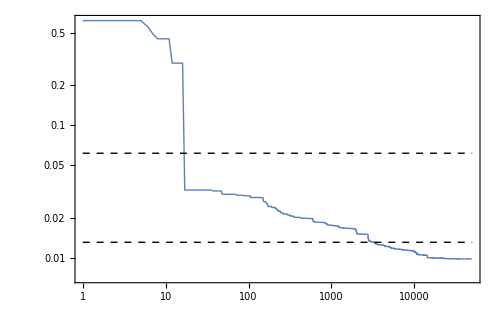

```mathematica
(* Plot of χ^2 over the generations -> See Fig. 5 *)
ListLogLogPlot[DataElite//Abs,Joined->True,
PlotRange->{{1,generations},All},PlotStyle->Thick,
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"\\text{Generations}","\\chi^2"},BaseStyle->{FontFamily->"Times",FontSize->13},RotateLabel->False,
Epilog->{{Dashed,Line[{{1,0.061574},{generations,0.061574}}//Log],Line[{{1,0.0131214},{generations,0.0131214}}//Log]},Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{BBKS}"],Scaled[{0.75,0.51}]],Text[(MaTeX[#,Magnification->1.4]&)/@Style["\\text{Eisenstein-Hu}"], Scaled[{0.18, 0.19}]]},ImageSize->500]
```

```mathematica
(* Make up the winner for presentation *)
χ2GA[Winner[x,y,z]]
χ2GA[(1-x-x^2 (-12.61 y^0.061 z^1.77+0.93 y^0.115 z^0.005 Log[x]^2+(y^0.1314 (0.359 z^0.00326+0.334 z^0.0043)-2.238 z^1.105-71.598 z^3.876) Log[x]^4-0.702 y^0.1458 z^0.186 Log[x]^5-0.973 y^0.231 z^1.2453 Log[x]^6))^12]
```

0.0098275

0.00982492

```mathematica
(* The Winner! *)
```

```mathematica
(1-x-x^2 (-12.61 y^0.061 z^1.77+0.93 y^0.115 z^0.005 Log[x]^2+(y^0.1314 (0.359 z^0.00326+0.334 z^0.0043)-2.238 z^1.105-71.598 z^3.876) Log[x]^4-0.702 y^0.1458 z^0.186 Log[x]^5-0.973 y^0.231 z^1.2453 Log[x]^6))^12/.x->k/.y->ωb/.z->ωm
```

(1-k-k^2 (-12.61 ωb^0.061 ωm^1.77+0.93 ωb^0.115 ωm^0.005 Log[k]^2+(ωb^0.1314 (0.359 ωm^0.00326+0.334 ωm^0.0043)-2.238 ωm^1.105-71.598 ωm^3.876) Log[k]^4-0.702 ωb^0.1458 ωm^0.186 Log[k]^5-0.973 ωb^0.231 ωm^1.2453 Log[k]^6))^12

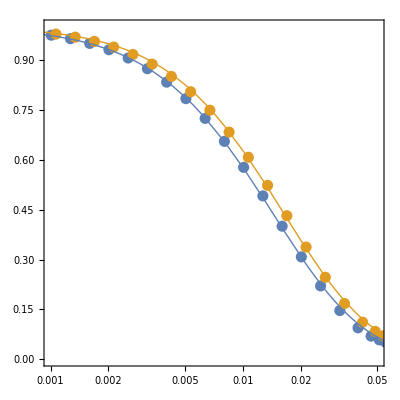

```mathematica
(* Best-Fit from the GA and the true function -> See Fig. 6 *)
LogLinearPlot[{Winner[k,NormPartData⟦1⟧⟦1,2⟧,NormPartData⟦1⟧⟦1,3⟧],Winner[k,NormPartData⟦16⟧⟦1,2⟧,NormPartData⟦16⟧⟦1,3⟧]}//Evaluate,{k,10^-5,1.2},PlotRange->All,PlotStyle->{Directive[Thick],Directive[Thick]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T^2(k)"},
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"]},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[{Table[{NormPartData⟦1⟧⟦i,1⟧,NormPartData⟦1⟧⟦i,4⟧},{i,1,Length[NormPartData⟦1⟧]}],Table[{NormPartData⟦16⟧⟦i,1⟧,NormPartData⟦16⟧⟦i,4⟧},{i,1,Length[NormPartData⟦10⟧]}]},Joined->False,PlotRange->{{10^-3,0.05},All},Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T^2(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{PointSize[0.02]},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%]
```

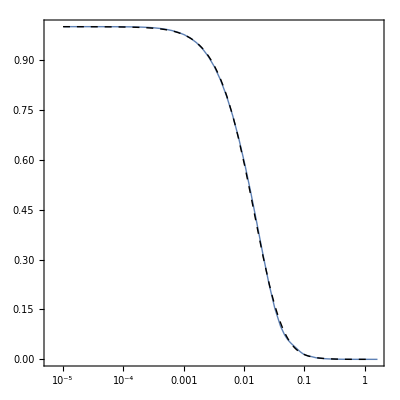

```mathematica
(* Best-Fit from the GA and the true function *)
LogLinearPlot[{Winner[k,NormPartData⟦10⟧⟦1,2⟧,NormPartData⟦10⟧⟦1,3⟧]}//Evaluate,{k,10^-5,1.2},PlotRange->All,PlotStyle->{Directive[Dashed,Thick,Black]},
Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"x"},
BaseStyle->{FontFamily->"Times",FontSize->13},Axes->False,AspectRatio->0.8,
PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{GA Solution}"]},LabelStyle->{Black,Bold,5}],
{0.23,0.1}]];
ListLogLinearPlot[Table[{NormPartData⟦10⟧⟦i,1⟧,NormPartData⟦10⟧⟦i,4⟧},{i,1,Length[NormPartData⟦1⟧]}],Joined->True,PlotRange->All,Frame->True,FrameStyle->BlackFrame,FrameLabel->(MaTeX[#,Magnification->18/12]&)/@{"k \\, [h \\, \\text{Mpc}^{-1}]","T^2(k)"},BaseStyle->{FontFamily->"Times",FontSize->13},PlotStyle->{Thick},AspectRatio->1,PlotLegends-> Placed[LineLegend[
{(MaTeX[#,Magnification->1.2]&)/@Style["\\text{CLASS Data}"]},LabelStyle->{Black,Bold,5}],
{0.26,0.2}]];
Show[%,%%]
```

## Comparison with BBKS and EH

## Fitting Formulae

### BBKS Fitting Formula

```mathematica
(* Various parameters *)
cH0 = 2997.92458; (* c/H0 [h^-1 Mpc] *)
Tcmb = 2.7255; (* CMB temperature [K] *)
h=0.67810; (* Reduced Hubble constant *)
Neff=3.046; (* Effective number of relativistic degrees of freedom *)
KtoeV = 8.621738*10^-5; (* Conversion from K to eV *)
(* BBKS: CDM >> Baryons, adiabatic fluctuations *)
ρcr[h_]:=8.098*10^-11 h^2; (* Critical density *)
Ωγ[h_]:=π^2/30 gγ*T^4/ρcr[h]/.T->Tcmb K/.gγ->2/.GeV->10^9/.K->KtoeV; (* Radiation density parameter *)
Ων[h_,Neff_]:=Neff*7/8 (4/11)^(4/3)Ωγ[h] (* Neutrinos density parameter *)
θ[h_,Neff_]:=(Ωγ[h]+Ων[h,Neff])/(1.68 Ωγ[h]) (* Measure of ρr/ργ *)
qBBKS[k_,ωb_,ωm_,h_,Neff_]:=(k*θ[h, Neff]^(1/2))/(ωm - ωb)
(* Transfer function for CDM *)
TcBBKS[k_,ωb_,ωm_,h_,Neff_]:=Log[1+2.34 qBBKS[k,ωb,ωm,h,Neff]]/(2.34 qBBKS[k, ωb, ωm, h, Neff])(1+3.89qBBKS[k,ωb,ωm,h,Neff] + (16.1 qBBKS[k,ωb,ωm,h,Neff])^2+(5.46 qBBKS[k,ωb,ωm,h,Neff])^3+(6.71 qBBKS[k,ωb,ωm,h,Neff])^4)^(-1/4)
(* BBKS: Non neglecteing baryons *)
RJr[ωb_,ωm_]:=1.6 (ωm-ωb)^(-1/2) (* Small scale filter [kpc] *)
TcbBBKS[k_,ωb_,ωm_,h_,Neff_]:=TcBBKS[k,ωb,ωm,h,Neff] (1+((10^-3*k*RJr[ωb, ωm])^2)/2)^-1 (* Transfer function for CDM + baryons *)
```

```mathematica
(* Fitness of the BBKS formula -> Remember the factor h for the units of k *)
Totχ2BBKS=Sum[(MockData⟦i,4⟧-TcbBBKS[MockData⟦i,1⟧*h,MockData⟦i,2⟧,MockData⟦i,3⟧,h,Neff]^2)^2,{i,1,Length[MockData]}]
χ2BBKS=Table[Sum[{(NormPartData⟦j⟧⟦i,4⟧-TcbBBKS[NormPartData⟦j⟧⟦i,1⟧*h,NormPartData⟦j⟧⟦1,2⟧,NormPartData⟦j⟧⟦1,3⟧,h,Neff]^2)^2},{i,1,Length[NormPartData⟦j⟧]}],{j,1,Length[NormPartData]}]
```

0.0615748

{{0.00331405},{0.00350539},{0.00389787},{0.00443635},{0.00345853},{0.00354344},{0.00385562},{0.00433406},{0.00366309},{0.00362977},{0.00385347},{0.00426513},{0.0039276},{0.00376653},{0.00389277},{0.0042311}}

### Eisenstein-Hu Fitting Formula

All the formulas are extracted from EH97I  [9709112 v1] paper, unless stated.

```mathematica
Θ=Solve[2.7*x==2.728]⟦1,1,2⟧;  (* Tcmb = 2.7Θ = 2.728 -> By FIRAS *)

(* See Eq. (11) *)
a1[ωm_]:=(46.9ωm)^0.670 (1+(32.1 ωm)^-0.532)
a2[ωm_]:=(12.0 ωm)^0.424 (1+(45.0 ωm)^-0.582) 
αc[ωb_,ωm_]:=a1[ωm]^(-ωb/ωm)*a2[ωm]^(-(ωb/ωm)^3)
(* See Eq. (12) *)
b1[ωm_] := 0.944 (1+(458 ωm)^-0.708)^-1 
b2[ωm_]:=(0.395 ωm)^-0.0266 
βc[ωb_,ωm_]:=(1+b1[ωm](((ωm - ωb)/ωm)^b2[ωm]-1))^-1 
(* Redshift at drag epoch -> See Eq. (4) *)
b1d[ωm_]:=0.313 ωm^-0.419 (1 + 0.607 ωm^0.674) 
b2d[ωm_]:=0.238 ωm^0.223 
zd[ωb_,ωm_]:=1291*ωm^0.251/(1 + 0.659 ωm^0.828)(1 + b1d[ωm] ωb^b2d[ωm]) 
zeq[ωm_]:=2.5*10^4 ωm*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (2) *)
keq[ωm_]:=7.46*10^-2 ωm*Θ^-2  (* scale at equilibrium epoch -> See Eq. (3) *)
q[k_,ωm_] := k/(13.41 keq[ωm])  (* See Eq. (10) *)
R[z_,ωb_]:=31.5*ωb*Θ^-4*(z/10^3)^-1  (* Baryon-Photon ratio -> See Eq. (5) *)
yEH[z_,ωm_]:=(1+zeq[ωm])/(1+z) (* Useful variable for calculations in LS limit -> See Eq.(8.20) in Dodelson 2 *)
(* Sub-horizon solution of the Mezsaros' eq. -> See Eq. (8.63) in Dodelson 2 *)
G[z_,ωm_]:=yEH[z, ωm] (-6 √(1+yEH[z,ωm])+(2+3yEH[z,ωm])Log[(√(1 + yEH[z, ωm])+1)/(√(1 + yEH[z, ωm])-1)]) 
(* Silk damping scale -> See Eq. (7) *)
ksilk[ωb_,ωm_]:=1.6 ωb^0.52*ωm^0.73(1+(10.4 ωm)^-0.95) (* [(Mpc^-1)]*)
βnode[ωm_]:=8.41*ωm^0.435 (* Shifting of nodes parameter -> See Eq. (23) *)
(* Sound horizon at drag epoch -> See Eq. (6) *)
s[ωb_,ωm_]:=2/(3 keq[ωm])√(6/R[zeq[ωm],ωb])Log[(√(1+R[zd[ωb,ωm],ωb])+√(R[zd[ωb,ωm],ωb]+R[zeq[ωm],ωb]))/(1+√R[zeq[ωm],ωb])]
st[k_,ωb_,ωm_]:=s[ωb,ωm]/((1+(βnode[ωm]/(k*s[ωb, ωm]))^3)^(1/3)) (* Shifting of oscillations nodes -> See Eq. (22) *)
(* Amplitude of small scale contributions -> See Eq. (14) *)
αb[ωb_,ωm_]:=2.07*keq[ωm]*s[ωb,ωm] (1+R[zd[ωb,ωm],ωb])^(-3/4)G[yEH[zd[ωb,ωm],ωm], ωm] 

(* Small scale contributions -> See Eq. (24) *)
βb[ωb_,ωm_]:=0.5+ωb/ωm+(3-2 ωb/ωm) √((17.2 ωm)^2+1)
f[k_,ωb_,ωm_]:=1/(1 + ((k*s[ωb, ωm])/5.4)^4) (* See Eq (18) *)
Cf[k_,ωb_,ωm_]:=14.2/αc[ωb,ωm]+386/(1 + 69.9*q[k,ωm]^1.08) (* See Eq. (20) *)
Cfαc1[k_,ωb_,ωm_]:=14.2 + 386/(1 + 69.9*q[k,ωm]^1.08) (* Cf with αc = 1*)
(* See Eq. (19) *)
T0[k_,ωb_,ωm_]:=Log[ⅇ + 1.8*βc[ωb,ωm]*q[k,ωm]]/(Log[ⅇ+1.8 βc[ωb,ωm]*q[k,ωm]]+Cf[k,ωb,ωm]*q[k,ωm]^2)
(* See Eqs. (19) and (20) in EH97: T0(k, 1, βc) means αc = 1 in Eq. (20) *)
T01[k_,ωb_,ωm_]:=Log[ⅇ+1.8*βc[ωb,ωm]*q[k,ωm]]/(Log[ⅇ + 1.8 βc[ωb,ωm]*q[k,ωm]]+Cfαc1[k,ωb,ωm]*q[k,ωm]^2)
(* See Eq. (19) in EH97: T0(k, 1, 1) means αc = 1 in Eq. (20) and βc = 1 in Eq. (19) *)
T011[k_,ωb_,ωm_]:=Log[ⅇ+1.8*q[k,ωm]]/(Log[E+1.8*q[k,ωm]]+Cfαc1[k,ωb,ωm]*q[k,ωm]^2)
(* Transfer function for CDM -> See Eq. (17) *)
TcEH[k_,ωb_,ωm_]:=f[k,ωb,ωm]*T01[k,ωb,ωm]+(1-f[k,ωb,ωm])T0[k,ωb,ωm]
(* Transfer function for baryons -> See Eq. (21) *)
TbEH[k_,ωb_,ωm_]:=(T011[k, ωb, ωm]/(1+((k*s[ωb,ωm])/5.2)^2)+αb[ωb,ωm]/(1 + (βb[ωb,ωm]/(k*s[ωb,ωm]))^3)ⅇ^(-(k/ksilk[ωb,ωm])^1.4))Sin[k*st[k,ωb,ωm]]/(k*st[k,ωb,ωm])
(* Transfer function for CDM + baryons -> See Eq. (16) *)
TEH[k_,ωb_,ωm_] := (ωm - ωb)/ωm TcEH[k,ωb,ωm]+ωb/ωm TbEH[k,ωb,ωm]
```

```mathematica
(* Fitness of the EH formula *)
Totχ2EH=Sum[(MockData⟦i,4⟧-TEH[MockData⟦i,1⟧*h,MockData⟦i,2⟧,MockData⟦i,3⟧]^2)^2,{i,1,Length[MockData]}]
χ2EH=Table[Sum[{(NormPartData⟦j⟧⟦i,4⟧-TEH[NormPartData⟦j⟧⟦i,1⟧*h,NormPartData⟦j⟧⟦1,2⟧,NormPartData⟦j⟧⟦1,3⟧]^2)^2},{i,1,Length[NormPartData⟦j⟧]}],{j,1,Length[NormPartData]}]
```

0.0131214

{{0.000861561},{0.000833381},{0.000808797},{0.000786971},{0.000859875},{0.000831637},{0.000806939},{0.00078476},{0.000858799},{0.000829989},{0.000805159},{0.000782936},{0.000857523},{0.000828466},{0.000803356},{0.000781267}}

### Eisenstein-Hu Fitting Formula: Massive Neutrinos

All the formulas are extracted from EH97I  [9710252] paper, unless stated.

```mathematica
zeqν[Ωm_,Ων_,h_]:=2.5*10^4(Ωm+Ων)h^2*Θ^-4 (* Redshift at equilibrium epoch -> See Eq. (1) *)
(* Redshift at drag epoch -> See Eq. (2) *)
b1dν[Ωm_,Ων_,h_]:=0.313((Ωm+Ων)h^2)^-0.419(1+0.607((Ωm+Ων)h^2)^0.674) 
b2dν[Ωm_,Ων_,h_]:=0.238((Ωm+Ων)h^2)^0.223 
zdν[Ωb_,Ωm_,Ων_,h_]:=1291*(((Ωm+Ων)h^2)^0.251)/(1+0.659((Ωm+Ων)h^2)^0.828)(1+b1dν[Ωm,Ων,h](Ωb*h^2)^b2dν[Ωm,Ων,h]) 
yEHν[z_,Ωm_,Ων_,h_]:=(1+zeqν[Ωm,Ων,h])/(1+z) (* Eq.(3) -> Useful variable for calculations in LS limit -> See Eq. (8.20) in Dodelson 2 *)
sν[Ωb_,Ωm_,Ων_,h_]:=(44.5Log[9.83/((Ωm+Ων)h^2)])/(√(1+10(Ωb*h^2)^(3/4))) (* Mpc *)(* Sound horizon at drag epoch -> See Eq. (4) *)
qν[k_,Ωm_,Ων_,h_]:=k*Θ^2((Ωm+Ων)h^2)^-1(* Mpc… See Eq. (5) *)
(* See Eq.(9)*)
g[z_,Ωm_,Ων_,ΩΛ_]:=√((Ωm+Ων)(1+z)^3+(1-Ωm-Ων-ΩΛ)(1+z)^2+ΩΛ)
(* See Eq.(10)*)
Ω[z_,Ωm_,Ων_,ΩΛ_]:=(Ωm+Ων)(1+z)^3 g[z,Ωm,Ων,ΩΛ]^-2
ΩΛf[z_,Ωm_,Ων_,ΩΛ_]:=ΩΛ*g[z,Ωm,Ων,ΩΛ]^-2
D1[z_,Ωm_,Ων_,ΩΛ_,h_]:=((1+zeqν[Ωm,Ων,h])/(1+z))*(5Ω[z,Ωm,Ων,ΩΛ])/2(Ω[z,Ωm,Ων,ΩΛ]^(4/7)-ΩΛf[z,Ωm,Ων,ΩΛ]+(1+Ω[z,Ωm,Ων,ΩΛ]/2)(1+ΩΛf[z,Ωm,Ων,ΩΛ]/70))^-1 
pcb[Ωm_,Ων_]:=1/4(5-√(1+24fcb[Ωm,Ων])) (* Eq.(11) *)
fcb[Ωm_,Ων_]:=Ωm/(Ωm+Ων)
fν[Ωm_,Ων_]:=Ων/(Ωm+Ων)
yfs[k_,Ωm_,Ων_,h_,Nν_]:=17.2*fν[Ωm,Ων](1+0.488*fν[Ωm,Ων]^(-7/6))*((Nν*qν[k,Ωm,Ων,h])/fν[Ωm,Ων])^2 (* Eq.(14) *) 
Dcbν[k_,z_,Ωm_,Ων_,ΩΛ_,h_,Nν_]:=(fcb[Ωm,Ων]^(0.7/pcb[Ωm,Ων])+(D1[z,Ωm,Ων,ΩΛ,h]/(1+yfs[k,Ωm,Ων,h,Nν]))^0.7)^(pcb[Ωm,Ων]/0.7)D1[z,Ωm,Ων,ΩΛ,h]^(1-pcb[Ωm,Ων]) (* Eq.(13) *)
qνν[k_,Ωm_,Ων_,h_,Nν_]:=3.92qν[k,Ωm,Ων,h]*√(Nν/fν[Ωm,Ων])(* Eq.(23) *)
B[k_,Ωm_,Ων_,h_,Nν_]:=1+(1.24 fν[Ωm,Ων]^0.64*Nν^(0.3+(0.6fν[Ωm,Ων])))/(qνν[k,Ωm,Ων,h,Nν]^-1.6+qνν[k,Ωm,Ων,h,Nν]^0.8) (* Eq.(22) *)
fνb[Ωb_,Ωm_,Ων_]:=(Ωb+Ων)/(Ωm+Ων)
βcν[Ωb_,Ωm_,Ων_]:=(1-0.949fνb[Ωb,Ωm,Ων])^-1(* Eq.(21) *)
C0[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=14.4+325/(1+60.5 qeff[k,Ωb,Ωm,Ων,h,Nν]^1.08)(* Eq.(20) *)
fc[Ωb_,Ωm_,Ων_]:=(Ωm-Ωb)/(Ωm+Ων)
pc[Ωb_,Ωm_,Ων_] :=1/4(5-√(1+24fc[Ωb,Ωm,Ων])) 
αν[Ωb_,Ωm_,Ων_,h_,Nν_]:=fc[Ωb,Ωm,Ων]/fcb[Ωm,Ων]*(5-2(pc[Ωb,Ωm,Ων]+pcb[Ωm,Ων]))/(5-4pcb[Ωm,Ων])*(1-0.553fνb[Ωb,Ωm,Ων]+0.126 fνb[Ωb,Ωm,Ων]^3)/(1-0.193 √(fν[Ωm,Ων]Nν)+0.169fν[Ωm,Ων] Nν^0.2) *(1+yEHν[zdν[Ωb,Ωm,Ων,h],Ωm,Ων,h])^(pcb[Ωm,Ων]-pc[Ωb,Ωm,Ων])*(1+(pc[Ωb,Ωm,Ων]-pcb[Ωm,Ων])/2(1+1/((3-4pc[Ωb,Ωm,Ων])(7-4pcb[Ωm,Ων])))(1+yEHν[zdν[Ωb,Ωm,Ων,h],Ωm,Ων,h])^-1)(* Eq.(15) *)
Γeff[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=(Ωm+Ων)h^2(√αν[Ωb,Ωm,Ων,h,Nν]+(1-√αν[Ωb,Ωm,Ων,h,Nν])/(1+(0.43 k*sν[Ωb,Ωm,Ων,h])^4)) (* Eq.(16) *)
qeff[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=(k*Θ^2)/Γeff[k,Ωb,Ωm,Ων,h,Nν](* Mpc… Eq.(17) *)
L[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=Log[ⅇ+1.84βcν[Ωb,Ωm,Ων] √αν[Ωb,Ωm,Ων,h,Nν] qeff[k,Ωb,Ωm,Ων,h,Nν]](* Eq.(19) *)
Tsup[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=L[k,Ωb,Ωm,Ων,h,Nν]/(L[k,Ωb,Ωm,Ων,h,Nν]+C0[k,Ωb,Ωm,Ων,h,Nν]*qeff[k,Ωb,Ωm,Ων,h,Nν]^2)(* Eq.(18) *) 
Tmaster[k_,Ωb_,Ωm_,Ων_,h_,Nν_]:=Tsup[k,Ωb,Ωm,Ων,h,Nν]*B[k,Ωm,Ων,h,Nν]
Tcbν[k_,z_,Ωb_,Ωm_,Ων_,ΩΛ_,h_,Nν_]:=Tmaster[k,Ωb,Ωm,Ων,h,Nν] Dcbν[k,z,Ωm,Ων,ΩΛ,h,Nν]/D1[z,Ωm,Ων,ΩΛ,h](* See Eq.(7) *)
```

```mathematica
DataGraνΦz0=Import["DataGraTz0_nu.txt","Data"]//Quiet;
Length[DataGraνΦz0]/114//N (* There are 27 lists *)
PartDataν=Partition[DataGraνΦz0,114]; (* Partition *)
NormPartDataν=Table[{#⟦1⟧,#⟦2⟧,#⟦3⟧,#⟦4⟧,((#⟦5⟧)/Max[PartDataν⟦i,1,5⟧])^2}&/@PartDataν⟦i⟧,{i,1,Length[PartDataν]}]; (* Normalized and squared data *)
MockDataν=Join@@NormPartDataν;
Dimensions[MockDataν]
```

64.

{7296,5}

```mathematica
(* mν ≠ 0 since some expressions goes to infinity -> For example, fν -> 0 and thus yfs -> ∞ *)
Totχ2EHν=Sum[(MockDataν⟦i,5⟧-Tcbν[MockDataν⟦i,1⟧*h,0,MockDataν⟦i,2⟧/h^2,MockDataν⟦i,3⟧/h^2,(MockDataν⟦i,4⟧+10^-10)/h^2,0.685,h,3]^2)^2,{i,1,Length[MockDataν]}]
χ2EHν=Table[Sum[{(NormPartDataν⟦j⟧⟦i,5⟧-Tcbν[NormPartDataν⟦j⟧⟦i,1⟧*h,0,(NormPartDataν⟦j⟧⟦1,2⟧)/h^2,(NormPartDataν⟦j⟧⟦1,3⟧)/h^2,(NormPartDataν⟦j⟧⟦1,4⟧+10^-10)/h^2,0.685,h,1]^2)^2},{i,1,Length[NormPartDataν⟦j⟧]}],{j,1,Length[NormPartDataν]}]
```

0.460223

{{0.00454724},{0.0061548},{0.00619135},{0.00597327},{0.00443695},{0.00600886},{0.00607081},{0.00587738},{0.00434032},{0.00587805},{0.00596235},{0.00579137},{0.00425607},{0.00576117},{0.00586505},{0.00571448},{0.0045657},{0.00617218},{0.00620915},{0.00599178},{0.00445479},{0.0060256},{0.00608799},{0.00589527},{0.00435749},{0.00589429},{0.00597895},{0.0058088},{0.00427253},{0.00577676},{0.00588127},{0.00573139},{0.00458396},{0.00618938},{0.00622676},{0.00600998},{0.00447228},{0.00604202},{0.00610492},{0.00591297},{0.0043741},{0.00590998},{0.00599539},{0.00582572},{0.00428842},{0.00579179},{0.00589683},{0.00574777},{0.00460195},{0.00620643},{0.00624414},{0.00602788},{0.00448944},{0.00605826},{0.00612159},{0.00593024},{0.00439053},{0.00592554},{0.00601126},{0.00584249},{0.00430414},{0.00580672},{0.00591223},{0.00576395}}

## Comparison

```mathematica
(* χ^2 for the 16 datasets *)
χ2TGA=Table[Sum[{(NormPartData⟦j⟧⟦i,4⟧-Winner[NormPartData⟦j⟧⟦i,1⟧,NormPartData⟦j⟧⟦1,2⟧,NormPartData⟦j⟧⟦1,3⟧])^2},{i,1,Length[NormPartData⟦j⟧]}],{j,1,Length[NormPartData]}]
```

{{0.000573534},{0.000517447},{0.000524778},{0.000638991},{0.000604431},{0.000557458},{0.000558926},{0.000656835},{0.000641954},{0.000601708},{0.0005967},{0.0006786},{0.000684793},{0.00065009},{0.000637435},{0.000703824}}

```mathematica
χ2BBKS
```

{{0.00331405},{0.00350539},{0.00389787},{0.00443635},{0.00345853},{0.00354344},{0.00385562},{0.00433406},{0.00366309},{0.00362977},{0.00385347},{0.00426513},{0.0039276},{0.00376653},{0.00389277},{0.0042311}}

```mathematica
χ2EH
```

{{0.000861561},{0.000833381},{0.000808797},{0.000786971},{0.000859875},{0.000831637},{0.000806939},{0.00078476},{0.000858799},{0.000829989},{0.000805159},{0.000782936},{0.000857523},{0.000828466},{0.000803356},{0.000781267}}

```mathematica
χ2EHν
```

{{0.00454724},{0.0061548},{0.00619135},{0.00597327},{0.00443695},{0.00600886},{0.00607081},{0.00587738},{0.00434032},{0.00587805},{0.00596235},{0.00579137},{0.00425607},{0.00576117},{0.00586505},{0.00571448},{0.0045657},{0.00617218},{0.00620915},{0.00599178},{0.00445479},{0.0060256},{0.00608799},{0.00589527},{0.00435749},{0.00589429},{0.00597895},{0.0058088},{0.00427253},{0.00577676},{0.00588127},{0.00573139},{0.00458396},{0.00618938},{0.00622676},{0.00600998},{0.00447228},{0.00604202},{0.00610492},{0.00591297},{0.0043741},{0.00590998},{0.00599539},{0.00582572},{0.00428842},{0.00579179},{0.00589683},{0.00574777},{0.00460195},{0.00620643},{0.00624414},{0.00602788},{0.00448944},{0.00605826},{0.00612159},{0.00593024},{0.00439053},{0.00592554},{0.00601126},{0.00584249},{0.00430414},{0.00580672},{0.00591223},{0.00576395}}

```mathematica
(* χ^2 for the 16 datasets, but comparing with T(k). The fitness is somewhat worse but its still good *)
χ2Linear=Table[Sum[{((NormPartData⟦j⟧⟦i,4⟧)^(1/2)-Winner[NormPartData⟦j⟧⟦i,1⟧,NormPartData⟦j⟧⟦1,2⟧,NormPartData⟦j⟧⟦1,3⟧]^(1/2))^2},{i,1,Length[NormPartData⟦j⟧]}],{j,1,Length[NormPartData]}]
```

{{0.00222343},{0.00198077},{0.0019152},{0.00183164},{0.00229772},{0.00204466},{0.00197169},{0.00188058},{0.00238072},{0.0021118},{0.00202915},{0.00193035},{0.0024727},{0.00218284},{0.00208726},{0.00198104}}